## Correlation energy tables for the effective potential

The effective potential is:
V(r)=1/r+∑_(i=0)^imax 1/l c_i (r/l)^i ⅇ^(-(r/l)^2).
Plug this into the Archer-Jain equation:

U≃e^2/(2ϵ l)∑_(i≠j) (∫_0^∞ V^eff Exp[-r^2/(4 l^2)] [I_0((r R_ij)/(2 l^2))-J_0((r R_ij)/(2 l^2))]rⅆr)/(4l sinh(R_ij^2/(4 l^2)))
to get the QM two-body energy.

The correlation energy calculation is the sum over all possible R_ij.

Reference:  “Maki-Zotos Correlation Energy Fig. 2 (7-27-13).nb”

Let a_0 be the distance between electrons, i.e. the lattice constant.  The unit cell is a parallelogram with an electron at its center.  This is the same parallelogram with an electron at each corner.  The area of the unit cell is a_c=(√3)/2 a_0^2.
Let N be the total number of electrons.

The charge density can be written as:  ρ=N/A=N/(N·a_c)=1/a_c.  Insert this into the definition of the filling factor, ν=2π l^2 ρ.
ν=2π l^2 ρ=(2 π l^2)/a_c.  Rearranging, a_c=(2π l^2)/ν.

Then express a_0 in terms of ν.
(√3)/2 a_0^2=(2π l^2)/ν
a_0=√((2π l^2)/ν 2/(√3))=√((4π l^2)/(√3 ν))

Reference:  "Bonsall, Maradudin eq. 2.18 derivation (5-17-14).nb"

Using our more accurate calculations, the Bonsall-Maradudin result for the ground-state correlation energy is
E_G=1/2 E_I=1/2(-3.92103157863978 . . .)e^2/(√a_c)=-0.78213263975429 . . .e^2/l √ν.  They had -3.921034.
I will use 8 digits, i.e. -0.78213264

The direct lattice vector of a hexagonal lattice is given by eq. 5 in Maki-Zotos:
OverVector[R_j]=a_0[n+m/2, (√3)/2 m]

Set the origin at <0,0>, i.e. m=0, n=0.  The reference electron will be set at the origin.  The equation produces all the points of a parallelogram.  The total shape will be a parallelogram.  The slope of the slant is √3.  For symmetry, m will run from -m_max… m_max and n will run from -n_max… n_max.  There are a total of (2 m_max+1)(2 n_max+1) electrons.

 |OverVector[R_i]|, the distance from the center electron to all other electrons, can be expressed as (where l→1; the l cancels out with l's in the denominators of the AJ equations):

```mathematica
R[m_,n_,ν_]:=√((4π)/(√3 ν))√((n+m/2)^2+((√3)/2 m)^2)
```

But in order to have a circular disk shape around the reference electron for maximum symmetry, we will have to limit the points to those within a certain radius.  A circle inscribed within a rhombus (where m_max=n_max) will have radius r=a_0(√3)/2 m_max.

```mathematica
circleradius[msize_,ν_]:=√((4π)/(√3 ν))(√3)/2 msize
```

Example:

```mathematica
circleradius[2,(4π)/(√3)]
```

√3

We count the total number of electrons.  We start with count=1 since the reference electron at the origin will not be included in the calculations.  Arbitrarily set ν=1 (ν just scales the distances).  Putting the count++ inside the energy summation doesn’t work when creating the table (not logical anyway).  So we just find the number of electrons inside the circle separately.  See “Electron Lattice.nb” in the LateX file (or somewhere else) for a graphical depiction.

```mathematica
numberofelectrons[msize_, nsize_]:=
For[m=-msize, m≤msize,m++,For[n=-nsize,n≤nsize,n++,If[R[m, n, 1]≤cradius,If[m==0&&n==0,0,count++;],0]]]
```

```mathematica
count=1;cradius=circleradius[2,1];numberofelectrons[2,2];count
```

13

```mathematica
count=1;cradius=circleradius[3,1];numberofelectrons[3,3];count
```

19

```mathematica
count=1;cradius=circleradius[50,1];numberofelectrons[50,50];count
```

6793

```mathematica
count=1;cradius=circleradius[100,1];numberofelectrons[100,100];count
```

27181

```mathematica
count=1;cradius=circleradius[200,1];numberofelectrons[200,200];count
```

108787

```mathematica
count=1;cradius=circleradius[650,1];numberofelectrons[650,650];count
```

1149427

```mathematica
count=1;cradius=circleradius[1000,1];numberofelectrons[1000,1000];count
```

2720557

```mathematica
(√3)/2*650//N
```

562.917

```mathematica
circleradius[650,ν]//N
```

1516.24 √(1/ν)

### Plots

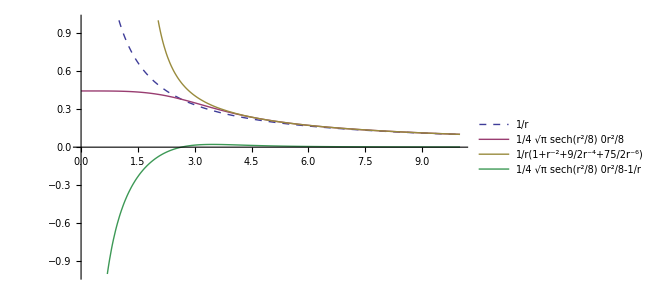

```mathematica
Plot[{1/r, (√π)/4 Sech[r^2/8]BesselI[0,r^2/8], 1/r(1+r^-2+9/2 r^-4+75/2 r^-6), (√π)/4 Sech[r^2/8]BesselI[0,r^2/8]-1/r},{r,0,10},PlotLegends->{1/r, TraditionalForm[(√π)/4 Sech[r^2/8]BesselI[0,r^2/8]], "1/r(1+r^-2+9/2r^-4+75/2r^-6)",TraditionalForm[(√π)/4 Sech[r^2/8]BesselI[0,r^2/8]-1/r ]},PlotRange->{-1, 1},PlotStyle->{Dashed,PointSize[1], PointSize[1], PointSize[1]}]
```

## 1.) The first term in the effective potential, 1/r, gives the Maki-Zotos result.

```mathematica
Assuming[Subscript[R, ij]∈Reals&&Subscript[R, ij]>0&&l∈Reals&&l>0,(∫_0^∞ 1/r Exp[-r^2/(4 l^2)](BesselI[0,r Subscript[R, ij]/(2 l^2)]-BesselJ[0,r Subscript[R, ij]/(2 l^2)])rⅆr)/(4l Sinh[Subscript[R, ij]^2/(4 l^2)])]//FullSimplify
```

1/4 √π BesselI[0,R_ij^2/(8 l^2)] Sech[R_ij^2/(8 l^2)]

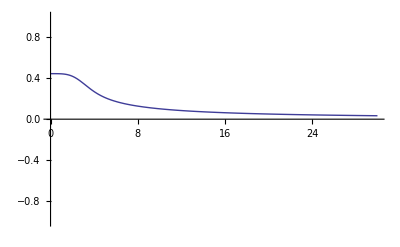

```mathematica
Plot[1/4 √π BesselI[0,Subscript[R, ij]^2/(8 l^2)] Sech[Subscript[R, ij]^2/(8 l^2)]/.l->1,{Subscript[R, ij], 0,30}, PlotRange->1]
```

The correlation energy as a function of filling factor is given by Fig. 2 in Maki-Zotos.  Their “R” is actually R/l.  All distances are from the origin.  Set l=1.

```mathematica
UCorMZ[msize_,nsize_,ν_]:=-0.78213264 ν^(1/2)+1/2∑_(m=-msize)^msize ∑_(n=-nsize)^nsize (If[R[m, n, ν]≤circleradius[msize, ν],If[m==0&&n==0,0,(R[m,n,ν])^-3+9/2(R[m,n,ν])^-5+75/2(R[m,n,ν])^-7],0])
```

```mathematica
TableMZ200= Parallelize[Table[{ν, UCorMZ[200,200, ν]}, {ν, 0.01, 1.0, 0.01}]]
```

{{0.01,-0.0779309},{0.02,-0.109809},{0.03,-0.133991},{0.04,-0.154141},{0.05,-0.171683},{0.06,-0.187349},{0.07,-0.201575},{0.08,-0.214646},{0.09,-0.226761},{0.1,-0.238063},{0.11,-0.248663},{0.12,-0.258645},{0.13,-0.268076},{0.14,-0.277012},{0.15,-0.285497},{0.16,-0.29357},{0.17,-0.301261},{0.18,-0.308598},{0.19,-0.315605},{0.2,-0.322302},{0.21,-0.328705},{0.22,-0.334831},{0.23,-0.340694},{0.24,-0.346305},{0.25,-0.351675},{0.26,-0.356814},{0.27,-0.361731},{0.28,-0.366433},{0.29,-0.370926},{0.3,-0.375219},{0.31,-0.379315},{0.32,-0.383221},{0.33,-0.386941},{0.34,-0.390479},{0.35,-0.39384},{0.36,-0.397025},{0.37,-0.40004},{0.38,-0.402887},{0.39,-0.405567},{0.4,-0.408085},{0.41,-0.410441},{0.42,-0.412638},{0.43,-0.414678},{0.44,-0.416562},{0.45,-0.418292},{0.46,-0.419869},{0.47,-0.421293},{0.48,-0.422567},{0.49,-0.423691},{0.5,-0.424666},{0.51,-0.425492},{0.52,-0.42617},{0.53,-0.426701},{0.54,-0.427085},{0.55,-0.427321},{0.56,-0.427412},{0.57,-0.427356},{0.58,-0.427153},{0.59,-0.426805},{0.6,-0.42631},{0.61,-0.425669},{0.62,-0.424881},{0.63,-0.423946},{0.64,-0.422865},{0.65,-0.421636},{0.66,-0.420259},{0.67,-0.418734},{0.68,-0.417061},{0.69,-0.415239},{0.7,-0.413267},{0.71,-0.411145},{0.72,-0.408872},{0.73,-0.406448},{0.74,-0.403871},{0.75,-0.401142},{0.76,-0.39826},{0.77,-0.395223},{0.78,-0.392031},{0.79,-0.388684},{0.8,-0.385179},{0.81,-0.381517},{0.82,-0.377697},{0.83,-0.373717},{0.84,-0.369576},{0.85,-0.365275},{0.86,-0.360811},{0.87,-0.356183},{0.88,-0.351391},{0.89,-0.346434},{0.9,-0.34131},{0.91,-0.336018},{0.92,-0.330558},{0.93,-0.324927},{0.94,-0.319126},{0.95,-0.313152},{0.96,-0.307005},{0.97,-0.300683},{0.98,-0.294185},{0.99,-0.28751},{1.,-0.280657}}

```mathematica
TableMZ200={{0.01,-0.07793093520809645},{0.02,-0.10980858137349987},{0.03,-0.1339907025500622},{0.04,-0.15414078889413646},{0.05,-0.17168262396838774},{0.060000000000000005,-0.1873485560780465},{0.07,-0.2015747635110417},{0.08,-0.21464608283319134},{0.09,-0.22676073986300332},{0.1,-0.23806328340292518},{0.11,-0.2486629605731652},{0.12,-0.258644706485713},{0.13,-0.2680760837520454},{0.14,-0.27701186047259196},{0.15,-0.2854971411648267},{0.16,-0.2935695737473291},{0.17,-0.3012609457894361},{0.18,-0.3085983649281623},{0.19,-0.3156051488111101},{0.2,-0.3223015075409584},{0.21000000000000002,-0.32870507494132806},{0.22000000000000003,-0.33483132772974455},{0.23,-0.3406939202648525},{0.24000000000000002,-0.346304954802587},{0.25,-0.351675201856043},{0.26,-0.35681428150017397},{0.27,-0.36173081378116734},{0.28,-0.36643254444676887},{0.29000000000000004,-0.3709264507859345},{0.30000000000000004,-0.3752188313041423},{0.31000000000000005,-0.37931538216169597},{0.32000000000000006,-0.38322126269489165},{0.33,-0.3869411518735364},{0.34,-0.39047929718695984},{0.35000000000000003,-0.3938395571683089},{0.36,-0.39702543854452854},{0.37,-0.4000401288229616},{0.38,-0.4028865249844855},{0.39,-0.40556725883967826},{0.4,-0.40808471951269876},{0.41000000000000003,-0.41044107344282077},{0.42000000000000004,-0.412638282232375},{0.43000000000000005,-0.4146781186194891},{0.44000000000000006,-0.41656218081236795},{0.45,-0.41829190538723876},{0.46,-0.41986857892319657},{0.47000000000000003,-0.42129334852295136},{0.48,-0.42256723134809404},{0.49,-0.4236911232802583},{0.5,-0.42466580680494},{0.51,-0.4254919582022811},{0.52,-0.4261701541185108},{0.53,-0.4267008775826016},{0.54,-0.42708452352488646},{0.55,-0.4273214038476129},{0.56,-0.42741175209157223},{0.5700000000000001,-0.4273557277378793},{0.5800000000000001,-0.42715342017956587},{0.5900000000000001,-0.4268048523938097},{0.6000000000000001,-0.42630998434227285},{0.61,-0.4256687161240633},{0.62,-0.42488089090327286},{0.63,-0.4239462976307508},{0.64,-0.4228646735777781},{0.65,-0.42163570669753264},{0.66,-0.4202590378286666},{0.67,-0.4187342627539158},{0.68,-0.41706093412543654},{0.6900000000000001,-0.41523856326744757},{0.7000000000000001,-0.41326662186578206},{0.7100000000000001,-0.41114454355306335},{0.7200000000000001,-0.4088717253974361},{0.73,-0.40644752930208555},{0.74,-0.40387128332211863},{0.75,-0.4011422829048445},{0.76,-0.39825979205893225},{0.77,-0.39522304445751516},{0.78,-0.3920312444798367},{0.79,-0.38868356819568833},{0.8,-0.38517916429653387},{0.81,-0.3815171549769051},{0.8200000000000001,-0.3776966367693607},{0.8300000000000001,-0.3737166813360692},{0.8400000000000001,-0.369576336219798},{0.85,-0.3652746255569272},{0.86,-0.36081055075486346},{0.87,-0.3561830911360987},{0.88,-0.351391204550941},{0.89,-0.3464338279608501},{0.9,-0.34130987799413287},{0.91,-0.33601825147564635},{0.92,-0.33055782593203753},{0.93,-0.3249274600739376},{0.9400000000000001,-0.31912599425644717},{0.9500000000000001,-0.3131522509191286},{0.9600000000000001,-0.30700503500667276},{0.97,-0.30068313437130895},{0.98,-0.29418532015795423},{0.99,-0.28751034717306134},{1.,-0.28065695423801607}};
```

```mathematica
TableMZ650=Parallelize[Table[{ν, UCorMZ[650,650, ν]}, {ν, 0.01, 1.0, 0.01}]]
```

{{0.01,-0.0779302},{0.02,-0.109806},{0.03,-0.133987},{0.04,-0.154135},{0.05,-0.171674},{0.06,-0.187338},{0.07,-0.201561},{0.08,-0.214629},{0.09,-0.226741},{0.1,-0.23804},{0.11,-0.248636},{0.12,-0.258614},{0.13,-0.268041},{0.14,-0.276973},{0.15,-0.285454},{0.16,-0.293522},{0.17,-0.301209},{0.18,-0.308542},{0.19,-0.315544},{0.2,-0.322235},{0.21,-0.328634},{0.22,-0.334755},{0.23,-0.340612},{0.24,-0.346218},{0.25,-0.351582},{0.26,-0.356716},{0.27,-0.361627},{0.28,-0.366323},{0.29,-0.370811},{0.3,-0.375097},{0.31,-0.379187},{0.32,-0.383087},{0.33,-0.3868},{0.34,-0.390332},{0.35,-0.393686},{0.36,-0.396865},{0.37,-0.399873},{0.38,-0.402713},{0.39,-0.405387},{0.4,-0.407897},{0.41,-0.410246},{0.42,-0.412436},{0.43,-0.414469},{0.44,-0.416346},{0.45,-0.418068},{0.46,-0.419637},{0.47,-0.421054},{0.48,-0.42232},{0.49,-0.423437},{0.5,-0.424403},{0.51,-0.425222},{0.52,-0.425892},{0.53,-0.426415},{0.54,-0.42679},{0.55,-0.427019},{0.56,-0.427101},{0.57,-0.427036},{0.58,-0.426826},{0.59,-0.426469},{0.6,-0.425965},{0.61,-0.425315},{0.62,-0.424519},{0.63,-0.423575},{0.64,-0.422485},{0.65,-0.421247},{0.66,-0.419861},{0.67,-0.418327},{0.68,-0.416645},{0.69,-0.414813},{0.7,-0.412832},{0.71,-0.410701},{0.72,-0.408418},{0.73,-0.405985},{0.74,-0.403399},{0.75,-0.40066},{0.76,-0.397768},{0.77,-0.394722},{0.78,-0.39152},{0.79,-0.388162},{0.8,-0.384648},{0.81,-0.380976},{0.82,-0.377146},{0.83,-0.373155},{0.84,-0.369005},{0.85,-0.364693},{0.86,-0.360219},{0.87,-0.355581},{0.88,-0.350779},{0.89,-0.345811},{0.9,-0.340676},{0.91,-0.335374},{0.92,-0.329903},{0.93,-0.324262},{0.94,-0.31845},{0.95,-0.312465},{0.96,-0.306307},{0.97,-0.299974},{0.98,-0.293465},{0.99,-0.286779},{1.,-0.279915}}

```mathematica
TableMZ650={{0.01,-0.07793019304999699},{0.02,-0.1098064822331976},{0.03,-0.13398684618271006},{0.04,-0.1541348516276189},{0.05,-0.17167432638537689},{0.060000000000000005,-0.18733764862086125},{0.07,-0.20156101854271632},{0.08,-0.2146292897010321},{0.09,-0.2267407015788203},{0.1,-0.23803981428272286},{0.11,-0.24863588448752794},{0.12,-0.2586138555200528},{0.13,-0.2680412971536218},{0.14,-0.27697298380504226},{0.15,-0.28545402561707944},{0.16,-0.2935220755600846},{0.17,-0.30120892577297587},{0.18,-0.3085416880523314},{0.19,-0.31554368385319265},{0.2,-0.3222351267806091},{0.21000000000000002,-0.3286336538941972},{0.22000000000000003,-0.3347547449132541},{0.23,-0.34061205699093955},{0.24000000000000002,-0.3462176949932565},{0.25,-0.35158243187836224},{0.26,-0.3567158900179559},{0.27,-0.36162669162107025},{0.28,-0.3663225844769226},{0.29000000000000004,-0.37081054780551376},{0.30000000000000004,-0.3750968819425495},{0.31000000000000005,-0.37918728478622454},{0.32000000000000006,-0.3830869173259023},{0.33,-0.38680046010631697},{0.34,-0.39033216211955507},{0.35000000000000003,-0.39368588333469856},{0.36,-0.3968651318526171},{0.37,-0.3998730964969065},{0.38,-0.4027126755109505},{0.39,-0.40538650191764825},{0.4,-0.4078969660065342},{0.41000000000000003,-0.41024623533826565},{0.42000000000000004,-0.4124362725952656},{0.43000000000000005,-0.4144688515569357},{0.44000000000000006,-0.41634557143620776},{0.45,-0.41806786977957844},{0.46,-0.41963703410387976},{0.47000000000000003,-0.4210542124188056},{0.48,-0.4223204227638208},{0.49,-0.42343656187085105},{0.5,-0.42440341304951323},{0.51,-0.42522165337921847},{0.52,-0.42589186028183446},{0.53,-0.4264145175394861},{0.54,-0.42679002081423784},{0.55,-0.42701868271964427},{0.56,-0.4271007374883106},{0.5700000000000001,-0.42703634527455003},{0.5800000000000001,-0.42682559612679527},{0.5900000000000001,-0.4264685136605983},{0.6000000000000001,-0.42596505845969296},{0.61,-0.42531513122964204},{0.62,-0.42451857572601304},{0.63,-0.42357518147676065},{0.64,-0.4224846863164754},{0.65,-0.4212467787483891},{0.66,-0.4198611001484602},{0.67,-0.4183272468244739},{0.68,-0.4166447719418349},{0.6900000000000001,-0.4148131873266443},{0.7000000000000001,-0.412831965155667},{0.7100000000000001,-0.410700539541898},{0.7200000000000001,-0.40841830802366946},{0.73,-0.40598463296452275},{0.74,-0.4033988428704262},{0.75,-0.4006602336303802},{0.76,-0.3977680696858794},{0.77,-0.39472158513431554},{0.78,-0.39151998477089284},{0.79,-0.38816244507333963},{0.8,-0.3846481151332864},{0.81,-0.3809761175379002},{0.8200000000000001,-0.377145549205086},{0.8300000000000001,-0.373155482175285},{0.8400000000000001,-0.36900496436267655},{0.85,-0.36469302026840594},{0.86,-0.36021865165818395},{0.87,-0.35558083820653946},{0.88,-0.35077853810972986},{0.89,-0.3458106886692515},{0.9,-0.3406762068476976},{0.91,-0.335373989798625},{0.92,-0.3299029153719469},{0.93,-0.32426184259627583},{0.9400000000000001,-0.31844961213955164},{0.9500000000000001,-0.312465046749166},{0.9600000000000001,-0.30630695167277133},{0.97,-0.29997411506080596},{0.98,-0.2934653083517774},{0.99,-0.286779286641218},{1.,-0.2799147890352056}};
```

```mathematica
Export["/home/ryan/Katsuaki's Files/Physics_MS_Thesis/Calculations/Effective Potentials (new)/TableMZ650.dat", TableMZ650]
```

/home/ryan/Katsuaki's Files/Physics_MS_Thesis/Calculations/Effective Potentials (new)/TableMZ650.dat

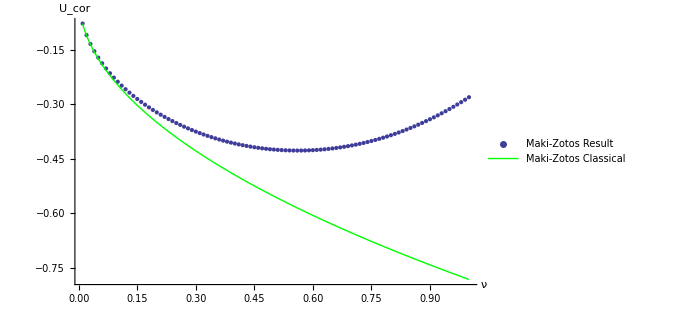

```mathematica
Show[ListPlot[TableMZ200,PlotLegends->{"Maki-Zotos Result"}],Plot[-0.78213264 √ν,{ν,0.01,1},PlotStyle->Green,PlotLegends->{"Maki-Zotos Classical"}],AxesLabel->{ν,"U_cor"},PlotRange->All,AxesOrigin->{0,0}]
```

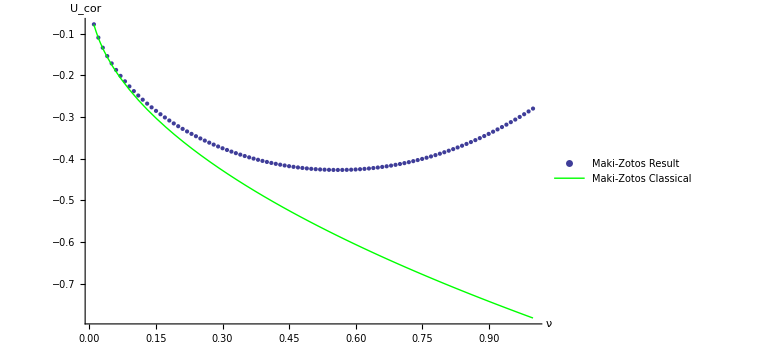

```mathematica
Show[ListPlot[TableMZ650,PlotLegends->{"Maki-Zotos Result"}],Plot[-0.78213264 √ν,{ν,0.01,1},PlotStyle->Green,PlotLegends->{"Maki-Zotos Classical"}],AxesLabel->{ν,"U_cor"},PlotRange->All,AxesOrigin->{0,0}]
```

(On the plot, the mmax=nmax=200 points are indistinguishable from the mmax=nmax=650 points.)

Take a look at what happens after ν=1.0:

```mathematica
TableMZ200ext= Parallelize[Table[{ν, UCorMZ[200,200, ν]}, {ν, 0.01, 5.0, 0.02}]]
```

{{0.01,-0.0779309},{0.03,-0.133991},{0.05,-0.171683},{0.07,-0.201575},{0.09,-0.226761},{0.11,-0.248663},{0.13,-0.268076},{0.15,-0.285497},{0.17,-0.301261},{0.19,-0.315605},{0.21,-0.328705},{0.23,-0.340694},{0.25,-0.351675},{0.27,-0.361731},{0.29,-0.370926},{0.31,-0.379315},{0.33,-0.386941},{0.35,-0.39384},{0.37,-0.40004},{0.39,-0.405567},{0.41,-0.410441},{0.43,-0.414678},{0.45,-0.418292},{0.47,-0.421293},{0.49,-0.423691},{0.51,-0.425492},{0.53,-0.426701},{0.55,-0.427321},{0.57,-0.427356},{0.59,-0.426805},{0.61,-0.425669},{0.63,-0.423946},{0.65,-0.421636},{0.67,-0.418734},{0.69,-0.415239},{0.71,-0.411145},{0.73,-0.406448},{0.75,-0.401142},{0.77,-0.395223},{0.79,-0.388684},{0.81,-0.381517},{0.83,-0.373717},{0.85,-0.365275},{0.87,-0.356183},{0.89,-0.346434},{0.91,-0.336018},{0.93,-0.324927},{0.95,-0.313152},{0.97,-0.300683},{0.99,-0.28751},{1.01,-0.273624},{1.03,-0.259013},{1.05,-0.243668},{1.07,-0.227578},{1.09,-0.210732},{1.11,-0.193118},{1.13,-0.174726},{1.15,-0.155543},{1.17,-0.135558},{1.19,-0.114759},{1.21,-0.0931331},{1.23,-0.0706691},{1.25,-0.047354},{1.27,-0.0231752},{1.29,0.0018803},{1.31,0.0278253},{1.33,0.0546731},{1.35,0.0824369},{1.37,0.11113},{1.39,0.140766},{1.41,0.171359},{1.43,0.202923},{1.45,0.235472},{1.47,0.269019},{1.49,0.303579},{1.51,0.339167},{1.53,0.375796},{1.55,0.413482},{1.57,0.45224},{1.59,0.492084},{1.61,0.533029},{1.63,0.575091},{1.65,0.618285},{1.67,0.662625},{1.69,0.708128},{1.71,0.754809},{1.73,0.802684},{1.75,0.851768},{1.77,0.902078},{1.79,0.953629},{1.81,1.00644},{1.83,1.06052},{1.85,1.11589},{1.87,1.17257},{1.89,1.23058},{1.91,1.28992},{1.93,1.35062},{1.95,1.41269},{1.97,1.47615},{1.99,1.54102},{2.01,1.60731},{2.03,1.67505},{2.05,1.74424},{2.07,1.81491},{2.09,1.88708},{2.11,1.96075},{2.13,2.03596},{2.15,2.11271},{2.17,2.19102},{2.19,2.27092},{2.21,2.35241},{2.23,2.43553},{2.25,2.52028},{2.27,2.60669},{2.29,2.69477},{2.31,2.78454},{2.33,2.87602},{2.35,2.96923},{2.37,3.06419},{2.39,3.16091},{2.41,3.25942},{2.43,3.35973},{2.45,3.46187},{2.47,3.56584},{2.49,3.67168},{2.51,3.7794},{2.53,3.88902},{2.55,4.00055},{2.57,4.11403},{2.59,4.22946},{2.61,4.34687},{2.63,4.46628},{2.65,4.58771},{2.67,4.71117},{2.69,4.83669},{2.71,4.96429},{2.73,5.09398},{2.75,5.22579},{2.77,5.35974},{2.79,5.49584},{2.81,5.63413},{2.83,5.77461},{2.85,5.91731},{2.87,6.06225},{2.89,6.20945},{2.91,6.35894},{2.93,6.51072},{2.95,6.66483},{2.97,6.82128},{2.99,6.98009},{3.01,7.14129},{3.03,7.3049},{3.05,7.47093},{3.07,7.63942},{3.09,7.81037},{3.11,7.98382},{3.13,8.15978},{3.15,8.33828},{3.17,8.51933},{3.19,8.70296},{3.21,8.8892},{3.23,9.07805},{3.25,9.26955},{3.27,9.46371},{3.29,9.66056},{3.31,9.86013},{3.33,10.0624},{3.35,10.2675},{3.37,10.4753},{3.39,10.6859},{3.41,10.8994},{3.43,11.1157},{3.45,11.3348},{3.47,11.5569},{3.49,11.7818},{3.51,12.0097},{3.53,12.2406},{3.55,12.4744},{3.57,12.7112},{3.59,12.9511},{3.61,13.194},{3.63,13.44},{3.65,13.6891},{3.67,13.9413},{3.69,14.1966},{3.71,14.4551},{3.73,14.7168},{3.75,14.9817},{3.77,15.2499},{3.79,15.5213},{3.81,15.796},{3.83,16.074},{3.85,16.3553},{3.87,16.64},{3.89,16.928},{3.91,17.2195},{3.93,17.5144},{3.95,17.8127},{3.97,18.1145},{3.99,18.4198},{4.01,18.7287},{4.03,19.0411},{4.05,19.357},{4.07,19.6766},{4.09,19.9998},{4.11,20.3266},{4.13,20.6571},{4.15,20.9913},{4.17,21.3292},{4.19,21.6708},{4.21,22.0162},{4.23,22.3655},{4.25,22.7185},{4.27,23.0754},{4.29,23.4361},{4.31,23.8008},{4.33,24.1693},{4.35,24.5419},{4.37,24.9183},{4.39,25.2988},{4.41,25.6833},{4.43,26.0719},{4.45,26.4645},{4.47,26.8612},{4.49,27.262},{4.51,27.667},{4.53,28.0762},{4.55,28.4896},{4.57,28.9071},{4.59,29.329},{4.61,29.7551},{4.63,30.1855},{4.65,30.6203},{4.67,31.0594},{4.69,31.5029},{4.71,31.9508},{4.73,32.4032},{4.75,32.86},{4.77,33.3213},{4.79,33.7871},{4.81,34.2575},{4.83,34.7324},{4.85,35.2119},{4.87,35.696},{4.89,36.1848},{4.91,36.6783},{4.93,37.1764},{4.95,37.6793},{4.97,38.187},{4.99,38.6994}}

```mathematica
TableMZ200ext={{0.01,-0.07793093520809645},{0.03,-0.1339907025500622},{0.05,-0.17168262396838774},{0.06999999999999999,-0.20157476351104167},{0.09,-0.22676073986300332},{0.11,-0.2486629605731652},{0.13,-0.2680760837520454},{0.15000000000000002,-0.28549714116482666},{0.17,-0.3012609457894361},{0.19,-0.3156051488111101},{0.21000000000000002,-0.32870507494132806},{0.23,-0.3406939202648525},{0.25,-0.351675201856043},{0.27,-0.36173081378116734},{0.29000000000000004,-0.3709264507859345},{0.31000000000000005,-0.37931538216169597},{0.33,-0.3869411518735364},{0.35000000000000003,-0.3938395571683089},{0.37,-0.4000401288229616},{0.39,-0.40556725883967826},{0.41000000000000003,-0.41044107344282077},{0.43000000000000005,-0.4146781186194891},{0.45,-0.41829190538723876},{0.47000000000000003,-0.42129334852295136},{0.49,-0.4236911232802583},{0.51,-0.4254919582022811},{0.53,-0.4267008775826016},{0.55,-0.4273214038476129},{0.57,-0.4273557277378792},{0.59,-0.4268048523938097},{0.61,-0.4256687161240633},{0.63,-0.4239462976307508},{0.65,-0.42163570669753264},{0.67,-0.4187342627539158},{0.6900000000000001,-0.41523856326744757},{0.71,-0.4111445435530633},{0.73,-0.40644752930208555},{0.75,-0.4011422829048445},{0.77,-0.39522304445751516},{0.79,-0.38868356819568833},{0.81,-0.3815171549769051},{0.8300000000000001,-0.3737166813360692},{0.8500000000000001,-0.3652746255569272},{0.8700000000000001,-0.3561830911360985},{0.89,-0.3464338279608501},{0.91,-0.33601825147564635},{0.93,-0.3249274600739376},{0.9500000000000001,-0.3131522509191286},{0.97,-0.30068313437130895},{0.99,-0.28751034717306134},{1.01,-0.2736238645279294},{1.03,-0.25901341118824817},{1.05,-0.2436684716546086},{1.07,-0.2275782995768285},{1.0899999999999999,-0.21073192643557037},{1.1099999999999999,-0.1931181695745574},{1.1300000000000001,-0.17472563964528187},{1.1500000000000001,-0.15554274751915087},{1.1700000000000002,-0.13555771071595646},{1.1900000000000002,-0.11475855939220747},{1.2100000000000002,-0.09313314192829292},{1.2300000000000002,-0.07066913014926834},{1.25,-0.04735402421054158},{1.27,-0.023175157176553607},{1.29,0.0018803006823026047},{1.31,0.027825337851684506},{1.33,0.054673097773636936},{1.35,0.08243687526660326},{1.37,0.11113011314824528},{1.3900000000000001,0.14076639904568955},{1.4100000000000001,0.1713594623792274},{1.4300000000000002,0.20292317150685557},{1.45,0.23547153101794904},{1.47,0.26901867916555944},{1.49,0.3035788854276422},{1.51,0.339166548188335},{1.53,0.37579619253118013},{1.55,0.41348246813679634},{1.5699999999999998,0.45224014727819695},{1.5899999999999999,0.4920841229073829},{1.61,0.5330294068274115},{1.6300000000000001,0.5750911279446065},{1.6500000000000001,0.6182845305959193},{1.6700000000000002,0.662624972946867},{1.6900000000000002,0.7081279254558015},{1.7100000000000002,0.7548089694006184},{1.73,0.8026837954642021},{1.75,0.8517682023753044},{1.77,0.9020780956016099},{1.79,0.9536294860921757},{1.81,1.0064384890664377},{1.83,1.060521322847325},{1.85,1.1158943077360206},{1.87,1.1725738649262807},{1.8900000000000001,1.23057651545613},{1.9100000000000001,1.289918879195105},{1.93,1.3506176738651787},{1.95,1.4126897140937045},{1.97,1.4761519104967733},{1.99,1.5410212687915492},{2.01,1.6073148889361106},{2.03,1.675049964295549},{2.05,1.744243780833093},{2.07,1.8149137163250624},{2.09,1.8870772395985531},{2.11,1.9607519097909223},{2.13,2.0359553756299604},{2.15,2.112705374733973},{2.17,2.1910197329308074},{2.19,2.2709163635950755},{2.21,2.352413267002756},{2.23,2.4355285297024962},{2.25,2.5202803239028717},{2.27,2.60668690687501},{2.29,2.6947666203699034},{2.31,2.7845378900498394},{2.33,2.876019224933441},{2.35,2.969229216853726},{2.37,3.064186539928718},{2.39,3.160909950044105},{2.4099999999999997,3.259418284347559},{2.4299999999999997,3.3597304607542138},{2.4499999999999997,3.46186547746289},{2.4699999999999998,3.5658424124827546},{2.4899999999999998,3.67168042316999},{2.51,3.7793987457741007},{2.53,3.8890166949935265},{2.55,4.000553663540367},{2.57,4.114029121713624},{2.59,4.229462616981001},{2.61,4.34687377356876},{2.63,4.466282292059439},{2.65,4.587707948997142},{2.67,4.711170596500223},{2.69,4.836690161881123},{2.71,4.964286647272972},{2.73,5.093980129262989},{2.75,5.225790758532325},{2.77,5.359738759502183},{2.79,5.495844429985983},{2.81,5.6341281408475155},{2.83,5.774610335664738},{2.85,5.917311530399219},{2.87,6.0622523130709105},{2.8899999999999997,6.209453343438236},{2.9099999999999997,6.358935352683246},{2.9299999999999997,6.510719143101696},{2.9499999999999997,6.664825587798029},{2.9699999999999998,6.821275630385031},{2.9899999999999998,6.980090284687957},{3.01,7.141290634453186},{3.03,7.304897833061236},{3.05,7.470933103243835},{3.07,7.6394177368052585},{3.09,7.810373094347585},{3.11,7.983820604999815},{3.13,8.159781766150827},{3.15,8.338278143186011},{3.17,8.519331369227611},{3.19,8.702963144878446},{3.21,8.889195237969039},{3.23,9.078049483308307},{3.25,9.26954778243738},{3.27,9.463712103386566},{3.29,9.660564480435555},{3.31,9.860127013876633},{3.33,10.062421869780847},{3.35,10.26747127976712},{3.3699999999999997,10.475297540774147},{3.3899999999999997,10.685923014835252},{3.4099999999999997,10.89937012885565},{3.4299999999999997,11.115661374392758},{3.4499999999999997,11.334819307438707},{3.4699999999999998,11.556866548205864},{3.4899999999999998,11.781825780914378},{3.51,12.009719753582559},{3.53,12.240571277819292},{3.55,12.474403228619225},{3.57,12.711238544159762},{3.59,12.951100225600761},{3.61,13.19401133688616},{3.63,13.439995004547752},{3.65,13.68907441751129},{3.67,13.941272826904372},{3.69,14.196613545866795},{3.71,14.455119949362267},{3.73,14.716815473992842},{3.75,14.981723617814533},{3.77,15.249867940155339},{3.79,15.521272061435077},{3.81,15.795959662986432},{3.83,16.073954486878794},{3.8499999999999996,16.355280335742883},{3.8699999999999997,16.639961072597828},{3.8899999999999997,16.92802062067943},{3.9099999999999997,17.219482963270277},{3.9299999999999997,17.51437214353157},{3.9499999999999997,17.812712264336362},{3.9699999999999998,18.114527488104663},{3.9899999999999998,18.419842036639672},{4.01,18.72868019096583},{4.029999999999999,19.041066291168427},{4.05,19.357024736234237},{4.069999999999999,19.676579983894477},{4.09,19.9997565504679},{4.109999999999999,20.326579010706492},{4.13,20.657071997641943},{4.1499999999999995,20.991260202433452},{4.17,21.329168374217314},{4.1899999999999995,21.670821319956993},{4.21,22.0162439042956},{4.2299999999999995,22.365461049408438},{4.25,22.718497734857845},{4.27,23.075378997448507},{4.29,23.43612993108451},{4.31,23.800775686627176},{4.329999999999999,24.169341471754375},{4.35,24.54185255082099},{4.369999999999999,24.91833424471992},{4.39,25.298811930745376},{4.409999999999999,25.683311042456157},{4.43,26.07185706954055},{4.45,26.464475557682235},{4.47,26.86119210842741},{4.49,27.262032379052464},{4.51,27.6670220824332},{4.53,28.076186986914955},{4.55,28.48955291618326},{4.57,28.907145749136443},{4.59,29.328991419758186},{4.609999999999999,29.75511591699148},{4.63,30.18554528461385},{4.6499999999999995,30.620305621113097},{4.67,31.05942307956363},{4.6899999999999995,31.502923867504805},{4.71,31.95083424681901},{4.7299999999999995,32.4031805336114},{4.749999999999999,32.85998909809004},{4.77,33.321286364447126},{4.789999999999999,33.78709881074119},{4.81,34.25745296877963},{4.829999999999999,34.732375424002925},{4.85,35.21189281536891},{4.87,35.69603183523751},{4.89,36.184819229258245},{4.91,36.67828179625591},{4.93,37.176446388118826},{4.95,37.679339909687265},{4.97,38.18698931864252},{4.99,38.69942162539723}};
```

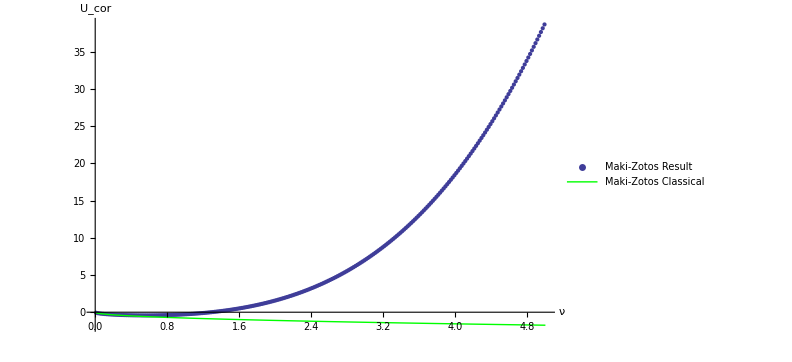

```mathematica
Show[ListPlot[TableMZ200ext,PlotLegends->{"Maki-Zotos Result"}],Plot[-0.78213264 √ν,{ν,0.01,5},PlotStyle->Green,PlotLegends->{"Maki-Zotos Classical"}],AxesLabel->{ν,"U_cor"},PlotRange->All,AxesOrigin->{0,0}]
```

So the energy rapidly becomes positive.

The Maki-Zotos approximation (eq. 19) to the two-body energy (eq. 9) doesn’t make sense.  Why do it?  They created the approximation just because it mostly fits the two-body energy curve and the 1/R term can be separated out.  The energy corresponding to this 1/R is replaced by the Bonsall-Maradudin energy.  The curve doesn’t fit for small R.  

We try a better method:
1.)  Use the entire two-body expression.  This is the full quantum-mechanical two-body energy.
2.)  Add the Bonsall-Maradudin classical energy result.  This contains the e-e, e-b, b-b energies.  Of course, B-M didn’t consider the b-b energy.
3.)  Subtract out the 1/R correlation energy.  But be careful:  
E_tot=1/2 N E_(1/R), so E_cor=E_tot/N=1/2 E_(1/R), where E_(1/R)=∑_i 1/R_i (the Coulomb energies between the reference electron and all surrounding electrons).

This has the effect of taking the QM e-e energy and adding the classical e-b and b-b energies.  The resulting curve is better . . . ?

```mathematica
UCorMZnew[msize_,nsize_,ν_]:=-0.78213264 ν^(1/2)+1/2∑_(m=-msize)^msize ∑_(n=-nsize)^nsize (If[R[m, n, ν]≤circleradius[msize, ν],If[m==0&&n==0,0,(√π BesselI[0,(R[m, n, ν])^2/8] Sech[(R[m, n, ν])^2/8])/4-1/R[m, n, ν]],0])
```

```mathematica
TableMZnew650= Parallelize[Table[{ν, UCorMZnew[650,650, ν]}, {ν, 0.01,1, 0.01}]]
```

{{0.01,-0.0779302},{0.02,-0.109806},{0.03,-0.133987},{0.04,-0.154135},{0.05,-0.171674},{0.06,-0.187337},{0.07,-0.20156},{0.08,-0.214627},{0.09,-0.226736},{0.1,-0.238032},{0.11,-0.248623},{0.12,-0.258595},{0.13,-0.268013},{0.14,-0.276932},{0.15,-0.285396},{0.16,-0.293443},{0.17,-0.301103},{0.18,-0.308403},{0.19,-0.315369},{0.2,-0.322019},{0.21,-0.328375},{0.22,-0.334453},{0.23,-0.34027},{0.24,-0.345841},{0.25,-0.351182},{0.26,-0.356308},{0.27,-0.361231},{0.28,-0.365966},{0.29,-0.370527},{0.3,-0.374925},{0.31,-0.379173},{0.32,-0.383284},{0.33,-0.387269},{0.34,-0.39114},{0.35,-0.394906},{0.36,-0.398579},{0.37,-0.402168},{0.38,-0.405683},{0.39,-0.409133},{0.4,-0.412526},{0.41,-0.41587},{0.42,-0.419172},{0.43,-0.42244},{0.44,-0.425679},{0.45,-0.428897},{0.46,-0.432097},{0.47,-0.435287},{0.48,-0.438469},{0.49,-0.441649},{0.5,-0.444831},{0.51,-0.448017},{0.52,-0.451212},{0.53,-0.454418},{0.54,-0.457637},{0.55,-0.460872},{0.56,-0.464124},{0.57,-0.467396},{0.58,-0.470689},{0.59,-0.474005},{0.6,-0.477343},{0.61,-0.480706},{0.62,-0.484093},{0.63,-0.487505},{0.64,-0.490944},{0.65,-0.494408},{0.66,-0.497898},{0.67,-0.501414},{0.68,-0.504956},{0.69,-0.508524},{0.7,-0.512118},{0.71,-0.515736},{0.72,-0.51938},{0.73,-0.523048},{0.74,-0.526739},{0.75,-0.530454},{0.76,-0.534192},{0.77,-0.537952},{0.78,-0.541734},{0.79,-0.545537},{0.8,-0.54936},{0.81,-0.553202},{0.82,-0.557064},{0.83,-0.560943},{0.84,-0.564841},{0.85,-0.568755},{0.86,-0.572686},{0.87,-0.576632},{0.88,-0.580593},{0.89,-0.584569},{0.9,-0.588558},{0.91,-0.59256},{0.92,-0.596575},{0.93,-0.600602},{0.94,-0.604639},{0.95,-0.608688},{0.96,-0.612746},{0.97,-0.616814},{0.98,-0.620891},{0.99,-0.624977},{1.,-0.629071}}

```mathematica
TableMZnew650={{0.01,-0.07793019285933375},{0.02,-0.10980647781694033},{0.03,-0.1339868181283573},{0.04,-0.15413474662815912},{0.05,-0.17167403213119886},{0.060000000000000005,-0.18733696151956974},{0.07,-0.20155960310812404},{0.08,-0.2146266277401945},{0.09,-0.22673602835565035},{0.1,-0.23803203837621253},{0.11,-0.2486234902849187},{0.12,-0.2585947943365395},{0.13,-0.2680128839519396},{0.14,-0.27693182700221974},{0.15,-0.28539602258430774},{0.16,-0.29344250379903475},{0.17,-0.30110265037353556},{0.18,-0.30840349295706226},{0.19,-0.31536872105903907},{0.2,-0.32201946644632756},{0.21000000000000002,-0.32837491071237557},{0.22000000000000003,-0.3344527522884321},{0.23,-0.3402695600681499},{0.24000000000000002,-0.3458410355915502},{0.25,-0.3511822020235738},{0.26,-0.356307535258009},{0.27,-0.3612310500353245},{0.28,-0.36596635182997095},{0.29000000000000004,-0.3705266633787011},{0.30000000000000004,-0.3749248330640831},{0.31000000000000005,-0.3791733309266587},{0.32000000000000006,-0.38328423684527146},{0.33,-0.3872692243846463},{0.34,-0.3911395429455069},{0.35000000000000003,-0.3949060001462455},{0.36,-0.3985789457960877},{0.37,-0.4021682583681794},{0.38,-0.4056833345284637},{0.39,-0.40913308200558013},{0.4,-0.4125259158837048},{0.41000000000000003,-0.41586975825120404},{0.42000000000000004,-0.41917204103234784},{0.43000000000000005,-0.42243971175811756},{0.44000000000000006,-0.4256792419875083},{0.45,-0.4288966380669124},{0.46,-0.4320974539066185},{0.47000000000000003,-0.43528680545668824},{0.48,-0.4384693865758403},{0.49,-0.44164948600412274},{0.5,-0.44483100517108976},{0.51,-0.44801747659435825},{0.52,-0.45121208264753987},{0.53,-0.45441767450090065},{0.54,-0.4576367910619461},{0.55,-0.460871677765917},{0.56,-0.46412430508780667},{0.5700000000000001,-0.467396386667559},{0.5800000000000001,-0.47068939695856443},{0.5900000000000001,-0.4740045883264198},{0.6000000000000001,-0.477343007539984},{0.61,-0.48070551161042796},{0.62,-0.4840927829458471},{0.63,-0.48750534379963273},{0.64,-0.4909435699998883},{0.65,-0.49440770395515304},{0.66,-0.49789786693842586},{0.67,-0.5014140706571291},{0.68,-0.5049562281215295},{0.6900000000000001,-0.5085241638279598},{0.7000000000000001,-0.5121176232763223},{0.7100000000000001,-0.5157362818439792},{0.7200000000000001,-0.5193797530399129},{0.73,-0.5230475961644852},{0.74,-0.5267393234011486},{0.75,-0.5304544063669608},{0.76,-0.5341922821490265},{0.77,-0.5379523588540768},{0.78,-0.5417340206979867},{0.79,-0.5455366326617573},{0.8,-0.549359544739823},{0.81,-0.5532020958058159},{0.8200000000000001,-0.5570636171202232},{0.8300000000000001,-0.5609434355033451},{0.8400000000000001,-0.5648408761961431},{0.85,-0.5687552654305309},{0.86,-0.572685932729719},{0.87,-0.5766322129581571},{0.88,-0.5805934481396691},{0.89,-0.5845689890613555},{0.9,-0.588558196679866},{0.91,-0.5925604433456697},{0.92,-0.596575113860061},{0.93,-0.6006016063786968},{0.9400000000000001,-0.6046393331745707},{0.9500000000000001,-0.6086877212726389},{0.9600000000000001,-0.612746212967245},{0.97,-0.6168142662330561},{0.98,-0.6208913550391789},{0.99,-0.6249769695756979},{1.,-0.6290706164010608}};
```

```mathematica
Export["/home/ryan/Katsuaki's Files/Physics_MS_Thesis/Calculations/Effective Potentials (new)/TableMZnew650.dat", TableMZnew650]
```

/home/ryan/Katsuaki's Files/Physics_MS_Thesis/Calculations/Effective Potentials (new)/TableMZnew650.dat

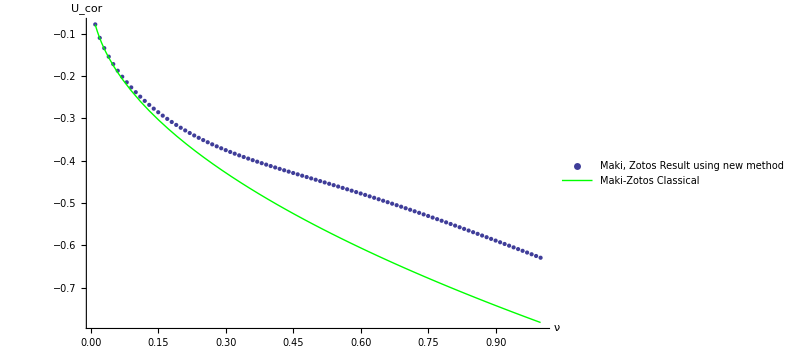

```mathematica
Show[ListPlot[TableMZnew650,PlotLegends->{"Maki, Zotos Result using 
new method"}],Plot[-0.78213264 √ν,{ν,0.01,1},PlotStyle->Green,PlotLegends->{"Maki-Zotos Classical"}],AxesLabel->{ν,"U_cor"},PlotRange->All,AxesOrigin->{0,0}]
```

### Try just adding the e-b and b-b parts instead:

E_(e-b)=∫(-eρ_+)/(|r⃗|)ⅆ^2 r=-e^2/a_c∫1/(|r⃗|)ⅆ^2 r
E_(b)=1/2∫(eρ_+)/(|r⃗|)ⅆ^2 r=e^2/(2 a_c)∫1/(|r⃗|)ⅆ^2 r
E_(e-b)+E_(b)=-(e^2 ν)/(2*2π l^2)2π R_max=-(e^2 ν)/(2 l^2)√((4π l^2)/(√3 ν))(√3)/2 m_max=-(e^2 √ν)/l 1/2 √((4π)/(√3))(√3)/2 m_max

Use m_max=650:

```mathematica
-1/2 √((4π)/(√3))(√3)/2*650//N
```

-758.121

```mathematica
UCorMZebb[msize_,nsize_,ν_]:=-758.1211470086542 ν^(1/2)+1/2∑_(m=-msize)^msize ∑_(n=-nsize)^nsize (If[R[m, n, ν]≤circleradius[msize, ν],If[m==0&&n==0,0,(√π BesselI[0,(R[m, n, ν])^2/8] Sech[(R[m, n, ν])^2/8])/4],0])
```

```mathematica
TableMZnewebb= Parallelize[Table[{ν, UCorMZebb[650,650, ν]}, {ν, 0.01,1, 0.02}]]
```

{{0.01,-0.0801842},{0.03,-0.137891},{0.05,-0.176714},{0.07,-0.207523},{0.09,-0.233498},{0.11,-0.256099},{0.13,-0.27614},{0.15,-0.294126},{0.17,-0.310396},{0.19,-0.325194},{0.21,-0.338704},{0.23,-0.35108},{0.25,-0.362452},{0.27,-0.372943},{0.29,-0.382665},{0.31,-0.391723},{0.33,-0.400218},{0.35,-0.408241},{0.37,-0.415879},{0.39,-0.42321},{0.41,-0.430303},{0.43,-0.43722},{0.45,-0.444017},{0.47,-0.45074},{0.49,-0.457428},{0.51,-0.464115},{0.53,-0.470827},{0.55,-0.477588},{0.57,-0.484414},{0.59,-0.491318},{0.61,-0.49831},{0.63,-0.505396},{0.65,-0.51258},{0.67,-0.519864},{0.69,-0.527248},{0.71,-0.534729},{0.73,-0.542306},{0.75,-0.549975},{0.77,-0.557731},{0.79,-0.565571},{0.81,-0.573488},{0.83,-0.581479},{0.85,-0.589536},{0.87,-0.597657},{0.89,-0.605834},{0.91,-0.614063},{0.93,-0.622339},{0.95,-0.630657},{0.97,-0.639014},{0.99,-0.647404}}

```mathematica
TableMZnewebb={{0.01,-0.08018423340124059},{0.03,-0.13789093086921866},{0.05,-0.17671422000699977},{0.06999999999999999,-0.20752323382714621},{0.09,-0.23349814998132956},{0.11,-0.25609929702469003},{0.13,-0.2761399427022866},{0.15,-0.29412588406438545},{0.17,-0.31039629761193055},{0.19,-0.32519385599545103},{0.21000000000000002,-0.33870422211481355},{0.23,-0.3510795587543498},{0.25,-0.3624524047324371},{0.27,-0.3729433882575677},{0.29000000000000004,-0.3826650431785197},{0.31000000000000005,-0.3917232975287561},{0.33,-0.40021770148547375},{0.35000000000000003,-0.40824108382582835},{0.37000000000000005,-0.41587905171707007},{0.39,-0.42320956067817406},{0.41000000000000003,-0.4303026598768156},{0.43000000000000005,-0.4372204440420546},{0.45,-0.44401720169395276},{0.47000000000000003,-0.4507397288668926},{0.49000000000000005,-0.4574277697954585},{0.51,-0.46411454579924794},{0.53,-0.47082733734032445},{0.55,-0.4775880898213245},{0.5700000000000001,-0.48441401956915797},{0.59,-0.49131820224920375},{0.61,-0.4983101310224356},{0.63,-0.5053962359551178},{0.65,-0.5125803597782124},{0.67,-0.5198641876535248},{0.6900000000000001,-0.5272476307809484},{0.7100000000000001,-0.5347291650442685},{0.7300000000000001,-0.5423061269963227},{0.7500000000000001,-0.5499749700718439},{0.77,-0.5577314843363865},{0.79,-0.565570983222301},{0.81,-0.5734884606830519},{0.8300000000000001,-0.581478722145448},{0.8500000000000001,-0.5895364924152773},{0.8700000000000001,-0.5976565034932264},{0.89,-0.6058335650027402},{0.91,-0.614062619688525},{0.93,-0.6223387861655283},{0.9500000000000001,-0.6306573908789233},{0.9700000000000001,-0.6390139910097332},{0.9900000000000001,-0.647404389795156}};
```

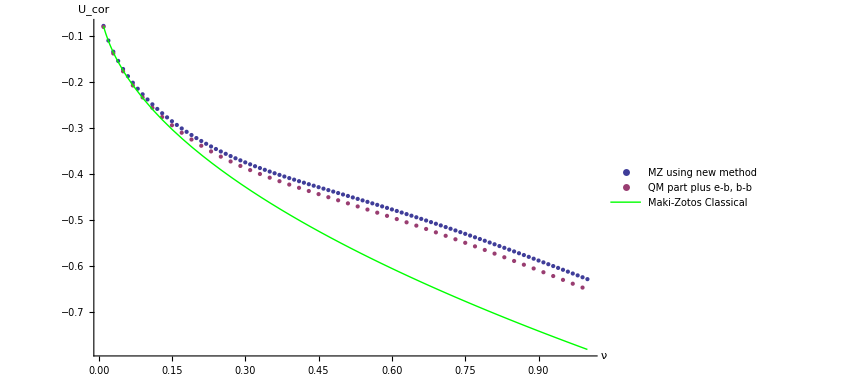

```mathematica
Show[ListPlot[{TableMZnew650,TableMZnewebb},PlotLegends->{"MZ using new method","QM part plus e-b, b-b"}],Plot[-0.78213264 √ν,{ν,0.01,1},PlotStyle->Green,PlotLegends->{"Maki-Zotos Classical"}],AxesLabel->{ν,"U_cor"},PlotRange->All,AxesOrigin->{0,0}]
```

Pretty good result.

### Try to recreate the classical curve (e-e+e-b+b):

E_(e-b)=∫(-eρ_+)/(|r⃗|)ⅆ^2 r=-e^2/a_c∫1/(|r⃗|)ⅆ^2 r
E_(b)=1/2∫(eρ_+)/(|r⃗|)ⅆ^2 r=e^2/(2 a_c)∫1/(|r⃗|)ⅆ^2 r
E_(e-b)+E_(b)=-(e^2 ν)/(2*2π l^2)2π R_max=-(e^2 ν)/(2 l^2)√((4π l^2)/(√3 ν))(√3)/2 m_max=-(e^2 √ν)/l 1/2 √((4π)/(√3))(√3)/2 m_max

```mathematica
-1/2 √((4π)/(√3))(√3)/2*650//N
```

-758.121

```mathematica
UCorClassical[msize_,nsize_,ν_]:=-758.1211470086542 ν^(1/2)+1/2∑_(m=-msize)^msize ∑_(n=-nsize)^nsize (If[R[m, n, ν]≤circleradius[msize, ν],If[m==0&&n==0,0,1/R[m,n,ν]],0])
```

```mathematica
TableClassical650= Parallelize[Table[{ν, UCorClassical[650,650, ν]}, {ν, 0.01,1, 0.02}]]
```

{{0.01,-0.0804673},{0.03,-0.139373},{0.05,-0.17993},{0.07,-0.212896},{0.09,-0.241402},{0.11,-0.26688},{0.13,-0.290129},{0.15,-0.311649},{0.17,-0.331775},{0.19,-0.350749},{0.21,-0.368748},{0.23,-0.385908},{0.25,-0.402337},{0.27,-0.41812},{0.29,-0.43333},{0.31,-0.448023},{0.33,-0.462249},{0.35,-0.476051},{0.37,-0.489464},{0.39,-0.502518},{0.41,-0.515242},{0.43,-0.527659},{0.45,-0.539791},{0.47,-0.551656},{0.49,-0.563271},{0.51,-0.574651},{0.53,-0.585811},{0.55,-0.596762},{0.57,-0.607515},{0.59,-0.618081},{0.61,-0.62847},{0.63,-0.638689},{0.65,-0.648748},{0.67,-0.658653},{0.69,-0.668412},{0.71,-0.67803},{0.73,-0.687513},{0.75,-0.696867},{0.77,-0.706098},{0.79,-0.715209},{0.81,-0.724206},{0.83,-0.733092},{0.85,-0.741872},{0.87,-0.750549},{0.89,-0.759127},{0.91,-0.767609},{0.93,-0.775999},{0.95,-0.784298},{0.97,-0.792511},{0.99,-0.80064}}

```mathematica
TableClassical650={{0.01,-0.08046730454186957},{0.03,-0.13937345981437943},{0.05,-0.17993036292179454},{0.06999999999999999,-0.21289647648876553},{0.09,-0.24140191362536711},{0.11,-0.26687985705652295},{0.13,-0.2901289925243873},{0.15,-0.3116485304049661},{0.17,-0.33177519603503924},{0.19,-0.350748848757064},{0.21000000000000002,-0.36874751403126993},{0.23,-0.38590763571755815},{0.25,-0.4023365227090494},{0.27,-0.4181203794433941},{0.29000000000000004,-0.4333296965442628},{0.31000000000000005,-0.44802299060029327},{0.33,-0.46224947193877597},{0.35000000000000003,-0.4760509936003814},{0.37000000000000005,-0.4894635049814724},{0.39,-0.5025181558005443},{0.41000000000000003,-0.5152421480322573},{0.43000000000000005,-0.5276594027499755},{0.45,-0.5397910887647299},{0.47000000000000003,-0.551656046564517},{0.49000000000000005,-0.5632711317929306},{0.51,-0.5746514962239644},{0.53,-0.5858108195585601},{0.55,-0.5967615022040036},{0.5700000000000001,-0.607514826743909},{0.59,-0.6180810941243635},{0.61,-0.6284697392204635},{0.63,-0.6386894294674903},{0.65,-0.6487481495275915},{0.67,-0.6586532742770714},{0.6900000000000001,-0.6684116320930116},{0.7100000000000001,-0.6780295599149895},{0.7300000000000001,-0.6875129513823595},{0.7500000000000001,-0.6968672990727782},{0.77,-0.7060977317033803},{0.79,-0.7152090470058283},{0.81,-0.7242057408761866},{0.8300000000000001,-0.7330920333215545},{0.8500000000000001,-0.7418718915827185},{0.8700000000000001,-0.7505490508419825},{0.89,-0.7591270327957318},{0.91,-0.7676091623476395},{0.93,-0.7759985826802449},{0.9500000000000001,-0.7842982688500797},{0.9700000000000001,-0.7925110401266693},{0.9900000000000001,-0.8006395711697678}};
```

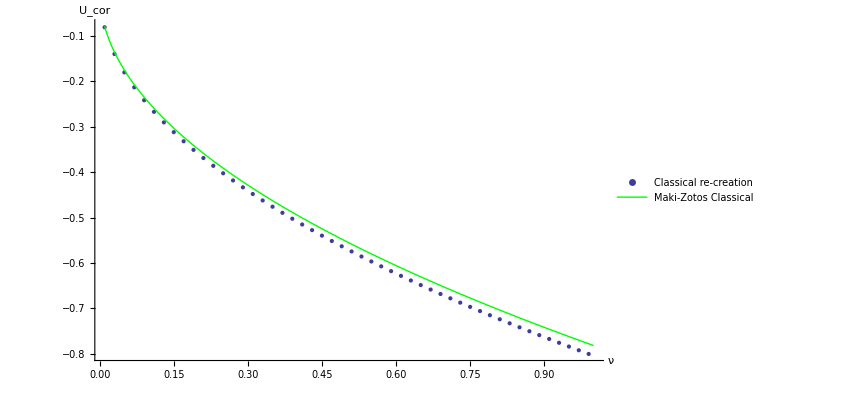

```mathematica
Show[ListPlot[TableClassical650,PlotLegends->{"Classical re-creation"}],Plot[-0.78213264 √ν,{ν,0.01,1},PlotStyle->Green,PlotLegends->{"Maki-Zotos Classical"}],AxesLabel->{ν,"U_cor"},PlotRange->All,AxesOrigin->{0,0}]
```

Pretty close

### Hole Lattice (MZ eq. 23)

```mathematica
Dataholenew650=AbsoluteTiming[Parallelize[Table[{ν,UCorMZnew[650,650,1-ν]-1/2 √(π/2)(2ν-1)},{ν, 0,0.99, 0.01}]]]
```

{3009.2021,{{0.,-0.00241355},{0.01,-0.010853},{0.02,-0.0193006},{0.03,-0.0277566},{0.04,-0.0362217},{0.05,-0.0446964},{0.06,-0.0531811},{0.07,-0.0616765},{0.08,-0.0701832},{0.09,-0.0787016},{0.1,-0.0872325},{0.11,-0.0957765},{0.12,-0.104334},{0.13,-0.112906},{0.14,-0.121493},{0.15,-0.130095},{0.16,-0.138714},{0.17,-0.14735},{0.18,-0.156003},{0.19,-0.164675},{0.2,-0.173365},{0.21,-0.182076},{0.22,-0.190806},{0.23,-0.199558},{0.24,-0.208331},{0.25,-0.217126},{0.26,-0.225944},{0.27,-0.234785},{0.28,-0.243651},{0.29,-0.25254},{0.3,-0.261455},{0.31,-0.270394},{0.32,-0.27936},{0.33,-0.288351},{0.34,-0.297368},{0.35,-0.306411},{0.36,-0.31548},{0.37,-0.324575},{0.38,-0.333695},{0.39,-0.342841},{0.4,-0.352012},{0.41,-0.361206},{0.42,-0.370424},{0.43,-0.379664},{0.44,-0.388925},{0.45,-0.398206},{0.46,-0.407504},{0.47,-0.416818},{0.48,-0.426146},{0.49,-0.435484},{0.5,-0.444831},{0.51,-0.454183},{0.52,-0.463536},{0.53,-0.472886},{0.54,-0.48223},{0.55,-0.491562},{0.56,-0.500878},{0.57,-0.510172},{0.58,-0.519437},{0.59,-0.528668},{0.6,-0.537857},{0.61,-0.546998},{0.62,-0.556081},{0.63,-0.565099},{0.64,-0.574043},{0.65,-0.582903},{0.66,-0.59167},{0.67,-0.600333},{0.68,-0.608881},{0.69,-0.617303},{0.7,-0.625588},{0.71,-0.633723},{0.72,-0.641695},{0.73,-0.649493},{0.74,-0.657103},{0.75,-0.664511},{0.76,-0.671703},{0.77,-0.678664},{0.78,-0.685381},{0.79,-0.691836},{0.8,-0.698014},{0.81,-0.703896},{0.82,-0.709464},{0.83,-0.714696},{0.84,-0.719569},{0.85,-0.724056},{0.86,-0.728125},{0.87,-0.731739},{0.88,-0.734854},{0.89,-0.737416},{0.9,-0.739358},{0.91,-0.740595},{0.92,-0.741019},{0.93,-0.740485},{0.94,-0.738795},{0.95,-0.735665},{0.96,-0.730659},{0.97,-0.723044},{0.98,-0.711397},{0.99,-0.692054}}}

```mathematica
Dataholenew650={{0.,-0.0024135477433107067},{0.01,-0.010853042291102843},{0.02,-0.01930056912773892},{0.03,-0.02775662169477111},{0.04,-0.0362217098021157},{0.05,-0.04469635948066386},{0.060000000000000005,-0.05318111275575066},{0.07,-0.061676527333031195},{0.08,-0.07018317618755099},{0.09,-0.07870164704631466},{0.1,-0.0872325417536659},{0.11,-0.09577647550831042},{0.12000000000000001,-0.104334075959779},{0.13,-0.11290598215142211},{0.14,-0.12149284329613896},{0.15,-0.13009531737010588},{0.16,-0.138714069508873},{0.16999999999999998,-0.14734977018923007},{0.18,-0.1560030931792632},{0.19,-0.16467471323801086},{0.2,-0.17336530354517293},{0.21000000000000002,-0.18207553284026234},{0.22,-0.19080606224964664},{0.23,-0.19955754177889173},{0.24,-0.2083306064469964},{0.25,-0.2171258720380858},{0.26,-0.2259439304454286},{0.27,-0.23478534458192013},{0.28,-0.24365064283050436},{0.29000000000000004,-0.2525403130077256},{0.30000000000000004,-0.2614547958132212},{0.31000000000000005,-0.2703944777380141},{0.32,-0.27935968340473916},{0.33,-0.28835066731349274},{0.34,-0.297367604967946},{0.35,-0.306410583357828},{0.36,-0.3154795907757183},{0.37,-0.3245745059486177},{0.38,-0.3336950864679871},{0.39,-0.342840956505723},{0.4,-0.3520115938084334},{0.41000000000000003,-0.3612063159680248},{0.42000000000000004,-0.37042426597332434},{0.43000000000000005,-0.37966439705547317},{0.44,-0.3889254568488767},{0.45,-0.398205970900142},{0.46,-0.40750422556932614},{0.47,-0.4168182503814356},{0.48,-0.42614579990122986},{0.49,-0.4354843352212032},{0.5,-0.44483100517108976},{0.51,-0.45418262737727777},{0.52,-0.4635356693221503},{0.53,-0.47288622957615317},{0.54,-0.48223001939923915},{0.55,-0.49156234493268813},{0.56,-0.5008780902264378},{0.5700000000000001,-0.5101717013702027},{0.5800000000000001,-0.5194371720175892},{0.5900000000000001,-0.5286680306095989},{0.6,-0.5378573296152548},{0.61,-0.5469976371102852},{0.62,-0.5560810310063238},{0.63,-0.5650990962191944},{0.64,-0.5740429250202578},{0.65,-0.5829031207435703},{0.66,-0.5916698049159865},{0.67,-0.6003326277282813},{0.68,-0.608880781562062},{0.6900000000000001,-0.6173030170166044},{0.7000000000000001,-0.625587660527184},{0.7100000000000001,-0.6337226322149558},{0.72,-0.6416954620393809},{0.73,-0.6494933016178895},{0.74,-0.6571029282137291},{0.75,-0.6645107363524488},{0.76,-0.671702711293581},{0.77,-0.6786643771433357},{0.78,-0.6853807107367721},{0.79,-0.69183601053387},{0.8,-0.6980137076409775},{0.81,-0.7038961036268445},{0.8200000000000001,-0.7094640168980224},{0.8300000000000001,-0.7146963156876509},{0.84,-0.7195693104863052},{0.85,-0.7240559706447325},{0.86,-0.7281249164357998},{0.87,-0.7317391147586747},{0.88,-0.7348541665164295},{0.89,-0.7374160038379635},{0.9,-0.7393576933024129},{0.91,-0.7405948246550054},{0.92,-0.7410185654127042},{0.93,-0.740484682153789},{0.9400000000000001,-0.7387951819383901},{0.9500000000000001,-0.7356653939231739},{0.96,-0.7306592497932892},{0.97,-0.7230444626666424},{0.98,-0.7113972637283804},{0.99,-0.6920541201439289}};
```

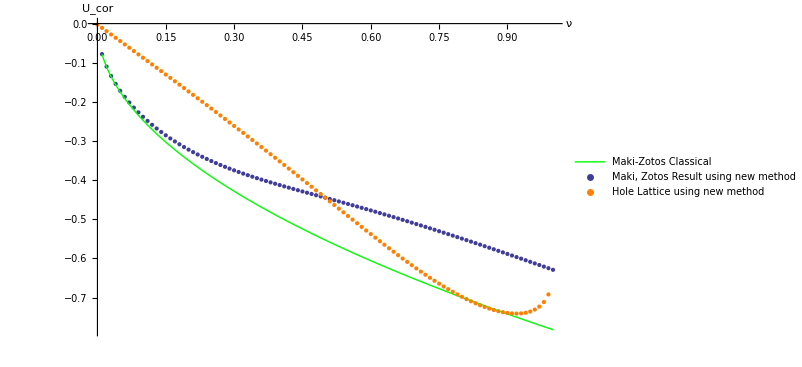

```mathematica
Show[ListPlot[TableMZnew650,PlotLegends->{"Maki, Zotos Result using 
new method"}],Plot[-0.78213264 √ν,{ν,0.01,1},PlotStyle->Green,PlotLegends->{"Maki-Zotos Classical"}],ListPlot[Dataholenew650,PlotStyle->Orange,PlotLegends->{"Hole Lattice using 
new method"}],AxesLabel->{ν,"U_cor"},PlotRange->All,AxesOrigin->{0,0}]
```

### Plot from ν=0.01 . . . 5.

```mathematica
TableMZnewext= Parallelize[Table[{ν, UCorMZnew[50,50,ν]}, {ν, 0.01,5, 0.02}]]
```

{{0.01,-0.0779342},{0.03,-0.134007},{0.05,-0.171718},{0.07,-0.201633},{0.09,-0.226843},{0.11,-0.248768},{0.13,-0.268198},{0.15,-0.285626},{0.17,-0.30138},{0.19,-0.315697},{0.21,-0.328756},{0.23,-0.340706},{0.25,-0.351677},{0.27,-0.361787},{0.29,-0.371145},{0.31,-0.379857},{0.33,-0.38802},{0.35,-0.395726},{0.37,-0.40306},{0.39,-0.410098},{0.41,-0.416909},{0.43,-0.423556},{0.45,-0.430092},{0.47,-0.436563},{0.49,-0.443008},{0.51,-0.44946},{0.53,-0.455946},{0.55,-0.462487},{0.57,-0.469101},{0.59,-0.475799},{0.61,-0.482592},{0.63,-0.489486},{0.65,-0.496483},{0.67,-0.503586},{0.69,-0.510794},{0.71,-0.518106},{0.73,-0.525518},{0.75,-0.533027},{0.77,-0.540628},{0.79,-0.548317},{0.81,-0.556089},{0.83,-0.563938},{0.85,-0.571859},{0.87,-0.579846},{0.89,-0.587894},{0.91,-0.595998},{0.93,-0.604154},{0.95,-0.612355},{0.97,-0.620598},{0.99,-0.628878},{1.01,-0.637192},{1.03,-0.645535},{1.05,-0.653904},{1.07,-0.662297},{1.09,-0.670709},{1.11,-0.679138},{1.13,-0.687581},{1.15,-0.696037},{1.17,-0.704504},{1.19,-0.712978},{1.21,-0.72146},{1.23,-0.729946},{1.25,-0.738436},{1.27,-0.746929},{1.29,-0.755424},{1.31,-0.763919},{1.33,-0.772414},{1.35,-0.780908},{1.37,-0.7894},{1.39,-0.797891},{1.41,-0.806379},{1.43,-0.814865},{1.45,-0.823347},{1.47,-0.831826},{1.49,-0.840302},{1.51,-0.848774},{1.53,-0.857243},{1.55,-0.865708},{1.57,-0.874169},{1.59,-0.882626},{1.61,-0.89108},{1.63,-0.899531},{1.65,-0.907977},{1.67,-0.916421},{1.69,-0.924861},{1.71,-0.933298},{1.73,-0.941732},{1.75,-0.950163},{1.77,-0.958592},{1.79,-0.967018},{1.81,-0.975441},{1.83,-0.983862},{1.85,-0.992281},{1.87,-1.0007},{1.89,-1.00911},{1.91,-1.01753},{1.93,-1.02594},{1.95,-1.03435},{1.97,-1.04276},{1.99,-1.05117},{2.01,-1.05957},{2.03,-1.06798},{2.05,-1.07639},{2.07,-1.08479},{2.09,-1.09319},{2.11,-1.1016},{2.13,-1.11},{2.15,-1.11841},{2.17,-1.12681},{2.19,-1.13521},{2.21,-1.14362},{2.23,-1.15202},{2.25,-1.16042},{2.27,-1.16883},{2.29,-1.17723},{2.31,-1.18563},{2.33,-1.19404},{2.35,-1.20244},{2.37,-1.21085},{2.39,-1.21926},{2.41,-1.22766},{2.43,-1.23607},{2.45,-1.24448},{2.47,-1.25289},{2.49,-1.2613},{2.51,-1.26971},{2.53,-1.27812},{2.55,-1.28653},{2.57,-1.29495},{2.59,-1.30336},{2.61,-1.31178},{2.63,-1.32019},{2.65,-1.32861},{2.67,-1.33703},{2.69,-1.34544},{2.71,-1.35386},{2.73,-1.36228},{2.75,-1.3707},{2.77,-1.37913},{2.79,-1.38755},{2.81,-1.39597},{2.83,-1.4044},{2.85,-1.41283},{2.87,-1.42125},{2.89,-1.42968},{2.91,-1.43811},{2.93,-1.44654},{2.95,-1.45497},{2.97,-1.4634},{2.99,-1.47183},{3.01,-1.48027},{3.03,-1.4887},{3.05,-1.49714},{3.07,-1.50557},{3.09,-1.51401},{3.11,-1.52245},{3.13,-1.53089},{3.15,-1.53933},{3.17,-1.54777},{3.19,-1.55621},{3.21,-1.56465},{3.23,-1.5731},{3.25,-1.58154},{3.27,-1.58999},{3.29,-1.59843},{3.31,-1.60688},{3.33,-1.61533},{3.35,-1.62377},{3.37,-1.63222},{3.39,-1.64067},{3.41,-1.64912},{3.43,-1.65758},{3.45,-1.66603},{3.47,-1.67448},{3.49,-1.68293},{3.51,-1.69139},{3.53,-1.69985},{3.55,-1.7083},{3.57,-1.71676},{3.59,-1.72522},{3.61,-1.73367},{3.63,-1.74213},{3.65,-1.75059},{3.67,-1.75905},{3.69,-1.76752},{3.71,-1.77598},{3.73,-1.78444},{3.75,-1.7929},{3.77,-1.80137},{3.79,-1.80983},{3.81,-1.8183},{3.83,-1.82676},{3.85,-1.83523},{3.87,-1.8437},{3.89,-1.85217},{3.91,-1.86064},{3.93,-1.86911},{3.95,-1.87758},{3.97,-1.88605},{3.99,-1.89452},{4.01,-1.90299},{4.03,-1.91146},{4.05,-1.91994},{4.07,-1.92841},{4.09,-1.93689},{4.11,-1.94536},{4.13,-1.95384},{4.15,-1.96232},{4.17,-1.97079},{4.19,-1.97927},{4.21,-1.98775},{4.23,-1.99623},{4.25,-2.00471},{4.27,-2.01319},{4.29,-2.02167},{4.31,-2.03015},{4.33,-2.03864},{4.35,-2.04712},{4.37,-2.0556},{4.39,-2.06409},{4.41,-2.07257},{4.43,-2.08106},{4.45,-2.08954},{4.47,-2.09803},{4.49,-2.10652},{4.51,-2.11501},{4.53,-2.12349},{4.55,-2.13198},{4.57,-2.14047},{4.59,-2.14896},{4.61,-2.15745},{4.63,-2.16595},{4.65,-2.17444},{4.67,-2.18293},{4.69,-2.19142},{4.71,-2.19992},{4.73,-2.20841},{4.75,-2.21691},{4.77,-2.2254},{4.79,-2.2339},{4.81,-2.2424},{4.83,-2.25089},{4.85,-2.25939},{4.87,-2.26789},{4.89,-2.27639},{4.91,-2.28489},{4.93,-2.29339},{4.95,-2.30189},{4.97,-2.31039},{4.99,-2.31889}}

```mathematica
TableMZnewext={{0.01,-0.07793415279434164},{0.03,-0.13400739460344915},{0.05,-0.1717183057622552},{0.06999999999999999,-0.2016329426568981},{0.09,-0.22684294762350565},{0.11,-0.24876796181695476},{0.13,-0.2681984973482607},{0.15000000000000002,-0.2856260778700636},{0.17,-0.30138021859846703},{0.19,-0.31569668629096126},{0.21000000000000002,-0.3287560005652666},{0.23,-0.34070636872382387},{0.25,-0.3516772081034747},{0.27,-0.3617866308048698},{0.29000000000000004,-0.3711451062590337},{0.31000000000000005,-0.37985684297870814},{0.33,-0.3880199402330218},{0.35000000000000003,-0.3957259886803648},{0.37,-0.4030595284696013},{0.39,-0.41009758748890346},{0.41000000000000003,-0.41690940216190775},{0.43000000000000005,-0.42355635013877707},{0.45,-0.4300920832795587},{0.47000000000000003,-0.4365628291312655},{0.49,-0.44300782166944713},{0.51,-0.4494598220374765},{0.53,-0.45594569389255946},{0.55,-0.46248700358337136},{0.57,-0.4691006214407869},{0.59,-0.47579930622965805},{0.61,-0.4825922599175353},{0.63,-0.4894856442190889},{0.65,-0.4964830538581546},{0.67,-0.5035859442104176},{0.6900000000000001,-0.5107940130414126},{0.71,-0.5181055375416777},{0.73,-0.5255176688868616},{0.75,-0.5330266872107071},{0.77,-0.540628220255629},{0.79,-0.5483174291295552},{0.81,-0.5560891646058915},{0.8300000000000001,-0.5639380973023091},{0.8500000000000001,-0.5718588248995652},{0.8700000000000001,-0.5798459593412576},{0.89,-0.5878941967107085},{0.91,-0.5959983722267667},{0.93,-0.604153502547533},{0.9500000000000001,-0.6123548173271065},{0.97,-0.6205977817404458},{0.99,-0.628878111478032},{1.01,-0.6371917815169494},{1.03,-0.6455350297984233},{1.05,-0.6539043567836462},{1.07,-0.6622965217190756},{1.0899999999999999,-0.6707085363180766},{1.1099999999999999,-0.6791376564568107},{1.1300000000000001,-0.687581372387098},{1.1500000000000001,-0.6960373978861817},{1.1700000000000002,-0.7045036586920611},{1.1900000000000002,-0.7129782805113055},{1.2100000000000002,-0.7214595768337508},{1.2300000000000002,-0.7299460367433612},{1.25,-0.7384363128763769},{1.27,-0.7469292096455464},{1.29,-0.7554236718219273},{1.31,-0.7639187735430799},{1.33,-0.7724137077973185},{1.35,-0.7809077764180103},{1.37,-0.789400380609004},{1.3900000000000001,-0.7978910120115754},{1.4100000000000001,-0.8063792443148151},{1.4300000000000002,-0.8148647254045545},{1.45,-0.8233471700404524},{1.47,-0.8318263530467436},{1.49,-0.8403021029989802},{1.51,-0.8487742963867713},{1.53,-0.8572428522308924},{1.55,-0.8657077271321273},{1.5699999999999998,-0.8741689107286001},{1.5899999999999999,-0.8826264215382054},{1.61,-0.8910803031628519},{1.6300000000000001,-0.8995306208315592},{1.6500000000000001,-0.9079774582600717},{1.6700000000000002,-0.9164209148053241},{1.6900000000000002,-0.9248611028938268},{1.7100000000000002,-0.933298145704064},{1.73,-0.9417321750838246},{1.75,-0.9501633296843697},{1.77,-0.958591753294332},{1.79,-0.9670175933572555},{1.81,-0.9754409996576046},{1.83,-0.983862123160967},{1.85,-0.9922811149952746},{1.87,-1.0006981255605687},{1.8900000000000001,-1.0091133037557727},{1.9100000000000001,-1.017526796311777},{1.93,-1.0259387472208688},{1.95,-1.034349297253326},{1.97,-1.0427585835526212},{1.99,-1.0511667393014543},{2.01,-1.059573893451323},{2.03,-1.0679801705090497},{2.05,-1.076385690374108},{2.07,-1.0847905682211756},{2.09,-1.0931949144228463},{2.11,-1.1015988345077286},{2.13,-1.1100024291497412},{2.15,-1.118405794184743},{2.17,-1.1268090206508379},{2.19,-1.1352121948493068},{2.21,-1.1436153984231778},{2.23,-1.152018708450793},{2.25,-1.1604221975520714},{2.27,-1.1688259340052605},{2.29,-1.177229981872342},{2.31,-1.185634401131259},{2.33,-1.1940392478135744},{2.35,-1.2024445741460417},{2.37,-1.2108504286949915},{2.39,-1.2192568565124058},{2.4099999999999997,-1.227663899282676},{2.4299999999999997,-1.2360715954693504},{2.4499999999999997,-1.2444799804610032},{2.4699999999999998,-1.2528890867156413},{2.4899999999999998,-1.2612989439031368},{2.51,-1.269709579045159},{2.53,-1.278121016652231},{2.55,-1.286533278857615},{2.57,-1.2949463855476369},{2.59,-1.3033603544883667},{2.61,-1.3117752014483715},{2.63,-1.3201909403174474},{2.65,-1.3286075832212008},{2.67,-1.3370251406314473},{2.69,-1.3454436214723549},{2.71,-1.3538630332223138},{2.73,-1.3622833820116003},{2.75,-1.3707046727157541},{2.77,-1.3791269090448095},{2.79,-1.3875500936284124},{2.81,-1.3959742280968679},{2.83,-1.404399313158199},{2.85,-1.4128253486713982},{2.87,-1.4212523337157936},{2.8899999999999997,-1.4296802666568478},{2.9099999999999997,-1.4381091452083201},{2.9299999999999997,-1.4465389664909858},{2.9499999999999997,-1.4549697270880457},{2.9699999999999998,-1.4634014230972985},{2.9899999999999998,-1.4718340501802016},{3.01,-1.4802676036079723},{3.03,-1.4887020783048275},{3.05,-1.49713746888846},{3.07,-1.505573769707895},{3.09,-1.5140109748788642},{3.11,-1.5224490783167337},{3.13,-1.5308880737671922},{3.15,-1.5393279548347476},{3.17,-1.5477687150091373},{3.19,-1.5562103476898066},{3.21,-1.564652846208493},{3.23,-1.5730962038500542},{3.25,-1.5815404138716356},{3.27,-1.5899854695202285},{3.29,-1.598431364048774},{3.31,-1.6068780907308224},{3.33,-1.6153256428738718},{3.35,-1.6237740138315035},{3.3699999999999997,-1.6322231970142707},{3.3899999999999997,-1.640673185899539},{3.4099999999999997,-1.6491239740402956},{3.4299999999999997,-1.6575755550729594},{3.4499999999999997,-1.6660279227242936},{3.4699999999999998,-1.674481070817544},{3.4899999999999998,-1.6829349932776552},{3.51,-1.6913896841359093},{3.53,-1.6998451375337627},{3.55,-1.7083013477261142},{3.57,-1.7167583090839753},{3.59,-1.7252160160966024},{3.61,-1.7336744633731098},{3.63,-1.7421336456436518},{3.65,-1.7505935577601641},{3.67,-1.759054194696728},{3.69,-1.767515551549566},{3.71,-1.7759776235367295},{3.73,-1.7844404059974965},{3.75,-1.7929038943914655},{3.77,-1.801368084297461},{3.79,-1.8098329714121926},{3.81,-1.8182985515487193},{3.83,-1.8267648206347555},{3.8499999999999996,-1.8352317747108071},{3.8699999999999997,-1.8436994099281865},{3.8899999999999997,-1.8521677225469169},{3.9099999999999997,-1.8606367089335036},{3.9299999999999997,-1.8691063655586555},{3.9499999999999997,-1.8775766889949228},{3.9699999999999998,-1.8860476759142526},{3.9899999999999998,-1.8945193230855366},{4.01,-1.9029916273720695},{4.029999999999999,-1.9114645857290615},{4.05,-1.9199381952010213},{4.069999999999999,-1.9284124529192344},{4.09,-1.9368873560991782},{4.109999999999999,-1.9453629020379626},{4.13,-1.95383908811178},{4.1499999999999995,-1.9623159117733655},{4.17,-1.970793370549499},{4.1899999999999995,-1.9792714620385172},{4.21,-1.9877501839078553},{4.2299999999999995,-1.9962295338916447},{4.25,-2.004709509788316},{4.27,-2.0131901094582885},{4.29,-2.0216713308216594},{4.31,-2.030153171855968},{4.329999999999999,-2.0386356305940088},{4.35,-2.047118705121667},{4.369999999999999,-2.055602393575836},{4.39,-2.0640866941423752},{4.409999999999999,-2.0725716050541205},{4.43,-2.0810571245889538},{4.45,-2.0895432510679193},{4.47,-2.0980299828533866},{4.49,-2.106517318347313},{4.51,-2.1150052559894976},{4.53,-2.1234937942559435},{4.55,-2.1319829316572156},{4.57,-2.1404726667369385},{4.59,-2.1489629980702603},{4.609999999999999,-2.157453924262416},{4.63,-2.165945443947338},{4.6499999999999995,-2.17443755578629},{4.67,-2.1829302584666204},{4.6899999999999995,-2.191423550700471},{4.71,-2.1999174312235934},{4.7299999999999995,-2.2084118987942167},{4.749999999999999,-2.216906952191932},{4.77,-2.225402590216637},{4.789999999999999,-2.2338988116875207},{4.81,-2.24239561544211},{4.829999999999999,-2.250893000335311},{4.85,-2.259390965238553},{4.87,-2.267889509038919},{4.89,-2.2763886306383547},{4.91,-2.2848883289528747},{4.93,-2.293388602911849},{4.95,-2.3018894514572836},{4.97,-2.3103908735431746},{4.99,-2.3188928681348493}};
```

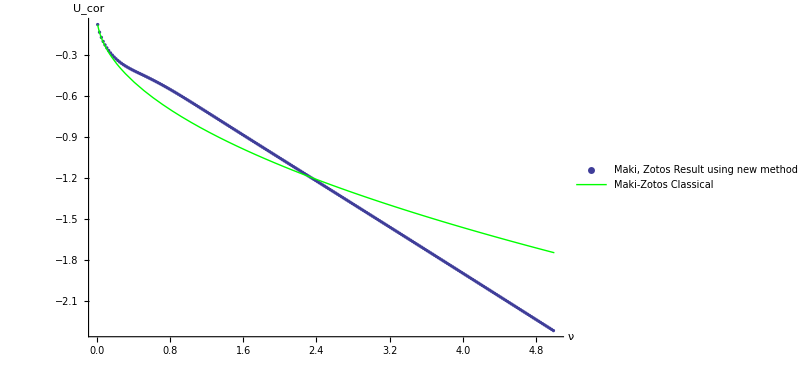

```mathematica
Show[ListPlot[TableMZnewext,PlotStyle->PointSize[0.004],PlotLegends->{"Maki, Zotos Result using 
new method"}],Plot[-0.78213264 √ν,{ν,0.01,5},PlotStyle->Green,PlotLegends->{"Maki-Zotos Classical"}],AxesLabel->{ν,"U_cor"},PlotRange->All,AxesOrigin->{0,0}]
```

Ok, so I’m not sure if this is ok, but at least it’s negative?

## 2.) The rest of the effective potential terms.

```mathematica
Clear[l]
```

```mathematica
Assuming[Subscript[R, ij]∈Reals&&Subscript[R, ij]>0&&l∈Reals&&l>0&&i∈Integers&&i≥0,(∫_0^∞ 1/l(r/l)^i Exp[-(r/l)^2]Exp[-r^2/(4 l^2)](BesselI[0,r Subscript[R, ij]/(2 l^2)]-BesselJ[0,r Subscript[R, ij]/(2 l^2)])rⅆr)/(4 l^2 Sinh[Subscript[R, ij]^2/(4 l^2)])]//FullSimplify
```

(2^(-2+i) 5^(-1-i/2) i Csch[R_ij^2/(4 l^2)] Gamma[i/2] (-Hypergeometric1F1[1+i/2,1,-R_ij^2/(20 l^2)]+Hypergeometric1F1[1+i/2,1,R_ij^2/(20 l^2)]))/l

Try 1/r^i

```mathematica
TryNegative[i_]:=Assuming[Subscript[R, ij]∈Reals&&Subscript[R, ij]>0&&l∈Reals&&l>0&&i∈Integers&&i≥0,(∫_0^∞ 1/l(r/l)^-i Exp[-(r/l)^2]Exp[-r^2/(4 l^2)](BesselI[0,r Subscript[R, ij]/(2 l^2)]-BesselJ[0,r Subscript[R, ij]/(2 l^2)])rⅆr)/(4 l^2 Sinh[Subscript[R, ij]^2/(4 l^2)])]//FullSimplify
```

```mathematica
l=1;
```

```mathematica
TryNegative[4]
```

Integrate::idiv: Integral of ⅇ^-5\ r^2/4\ BesselI[0, r\ R_ij/2]/r^3 - ⅇ^-5\ r^2/4\ BesselJ[0, r\ R_ij/2]/r^3 does not converge on {0, ∞}.

1/4 Csch[R_ij^2/4] ∫_0^∞ (ⅇ^(-(5 r^2)/4) (BesselI[0,(r R_ij)/2]-BesselJ[0,(r R_ij)/2]))/r^3 ⅆr

```mathematica
NIntegrate[2π(1/l(r/l)^-i Exp[-(r/l)^2]Exp[-r^2/(4 l^2)](BesselI[0,r Subscript[R, ij]/(2 l^2)]-BesselJ[0,r Subscript[R, ij]/(2 l^2)]))/(4 l^2 Sinh[Subscript[R, ij]^2/(4 l^2)])/.l->1/.Subscript[R, ij]->1/.i->4,{r,0,∞}]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in r near {r} = {1.0550418196256998801085166022336435412185594722445307083927206899×10^-29}. NIntegrate obtained 1.34134×10^31 and 1.23361×10^31 for the integral and error estimates.

1.34134×10^31

```mathematica
Plot[(1/l(r/l)^-i Exp[-(r/l)^2]Exp[-r^2/(4 l^2)](BesselI[0,r Subscript[R, ij]/(2 l^2)]-BesselJ[0,r Subscript[R, ij]/(2 l^2)]))/(4 l^2 Sinh[Subscript[R, ij]^2/(4 l^2)])/.l->1/.Subscript[R, ij]->1,{r,-5,5}, PlotRange->All]
```

-Graphics-

Doesn’t work.

A bit complicated.  Input i beforehand.

```mathematica
U[i_]:=Assuming[Subscript[R, ij]∈Reals&&Subscript[R, ij]>0&&l∈Reals&&l>0&&i∈Integers&&i≥0,(∫_0^∞ 1/l(r/l)^i Exp[-(r/l)^2]Exp[-r^2/(4 l^2)](BesselI[0,r Subscript[R, ij]/(2 l^2)]-BesselJ[0,r Subscript[R, ij]/(2 l^2)])rⅆr)/(4l Sinh[Subscript[R, ij]^2/(4 l^2)])]//FullSimplify
```

i=0:

```mathematica
U[0]
```

1/5 Csch[R_ij^2/(4 l^2)] Sinh[R_ij^2/(20 l^2)]

```mathematica
1/5 Csch[Subscript[R, ij]^2/(4 l^2)] Sinh[Subscript[R, ij]^2/(20 l^2)]/.l->1
```

1/5 Csch[R_ij^2/4] Sinh[R_ij^2/20]

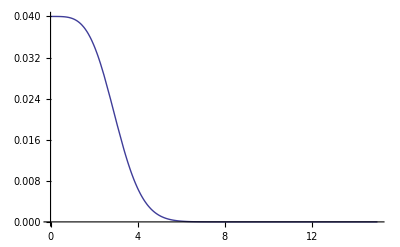

```mathematica
Plot[1/5 Csch[Subscript[R, ij]^2/4] Sinh[Subscript[R, ij]^2/20], {Subscript[R, ij],0,15}]
```

```mathematica
UCori0[msize_,nsize_,ν_]:=1/2∑_(m=-msize)^msize ∑_(n=-nsize)^nsize (If[R[m, n, ν]≤circleradius[msize, ν],If[m==0&&n==0,0,1/5 Csch[(R[m,n,ν])^2/4] Sinh[(R[m,n,ν])^2/20]],0])
```

```mathematica
Tablei0=AbsoluteTiming[Parallelize[Table[{ν,UCori0[650,650,ν]},{ν, 0.01,1, 0.01}]]]
```

{2413.93153,{{0.01,5.75847×10^-64},{0.02,1.85878×10^-32},{0.03,5.91838×10^-22},{0.04,1.05606×10^-16},{0.05,1.4948×10^-13},{0.06,1.88441×10^-11},{0.07,5.9647×10^-10},{0.08,7.95922×10^-9},{0.09,5.97079×10^-8},{0.1,2.99268×10^-7},{0.11,1.11857×10^-6},{0.12,3.35455×10^-6},{0.13,8.49151×10^-6},{0.14,0.0000188118},{0.15,0.0000374544},{0.16,0.0000683675},{0.17,0.000116169},{0.18,0.000185942},{0.19,0.000282995},{0.2,0.000412629},{0.21,0.00057991},{0.22,0.000789491},{0.23,0.00104547},{0.24,0.00135129},{0.25,0.00170968},{0.26,0.00212265},{0.27,0.00259148},{0.28,0.00311675},{0.29,0.00369843},{0.3,0.00433588},{0.31,0.00502796},{0.32,0.00577309},{0.33,0.00656933},{0.34,0.0074144},{0.35,0.00830583},{0.36,0.00924092},{0.37,0.0102169},{0.38,0.0112308},{0.39,0.0122798},{0.4,0.013361},{0.41,0.0144714},{0.42,0.0156082},{0.43,0.0167687},{0.44,0.0179502},{0.45,0.0191502},{0.46,0.0203662},{0.47,0.0215959},{0.48,0.0228373},{0.49,0.0240882},{0.5,0.0253467},{0.51,0.0266112},{0.52,0.0278799},{0.53,0.0291514},{0.54,0.0304243},{0.55,0.0316973},{0.56,0.0329694},{0.57,0.0342396},{0.58,0.0355068},{0.59,0.0367704},{0.6,0.0380296},{0.61,0.0392837},{0.62,0.0405323},{0.63,0.0417749},{0.64,0.0430111},{0.65,0.0442405},{0.66,0.0454629},{0.67,0.0466781},{0.68,0.047886},{0.69,0.0490863},{0.7,0.0502792},{0.71,0.0514644},{0.72,0.0526421},{0.73,0.0538123},{0.74,0.054975},{0.75,0.0561303},{0.76,0.0572784},{0.77,0.0584193},{0.78,0.0595533},{0.79,0.0606804},{0.8,0.0618009},{0.81,0.0629149},{0.82,0.0640226},{0.83,0.0651242},{0.84,0.06622},{0.85,0.06731},{0.86,0.0683946},{0.87,0.069474},{0.88,0.0705483},{0.89,0.0716177},{0.9,0.0726825},{0.91,0.0737429},{0.92,0.0747991},{0.93,0.0758512},{0.94,0.0768995},{0.95,0.0779442},{0.96,0.0789855},{0.97,0.0800234},{0.98,0.0810583},{0.99,0.0820903},{1.,0.0831196}}}

```mathematica
Tablei0={{0.01,5.7584663991852296*^-64},{0.02,1.8587845059369137*^-32},{0.03,5.918383628128748*^-22},{0.04,1.0560637641590488*^-16},{0.05,1.4947967707087756*^-13},{0.060000000000000005,1.8844071682612047*^-11},{0.07,5.964696560864723*^-10},{0.08,7.959223001185128*^-9},{0.09,5.970785828141957*^-8},{0.1,2.9926771981183353*^-7},{0.11,1.1185683135197586*^-6},{0.12,3.354554748443657*^-6},{0.13,8.49150693535728*^-6},{0.14,0.000018811834152061707},{0.15,0.00003745440360987338},{0.16,0.00006836751815671624},{0.17,0.00011616903760157797},{0.18,0.00018594154934833287},{0.19,0.0002829953142235656},{0.2,0.00041262881537652314},{0.21000000000000002,0.0005799097499547003},{0.22000000000000003,0.0007894911675527901},{0.23,0.0010454700224729863},{0.24000000000000002,0.0013512895448641847},{0.25,0.0017096827571765351},{0.26,0.0021226519988504114},{0.27,0.002591478143185585},{0.28,0.0031167529353580297},{0.29000000000000004,0.003698428227793035},{0.30000000000000004,0.0043358765825683605},{0.31000000000000005,0.005027958563128325},{0.32000000000000006,0.005773092922732734},{0.33,0.0065693267360624995},{0.34,0.007414403269861598},{0.35000000000000003,0.00830582602939632},{0.36,0.009240917946639454},{0.37,0.01021687509966642},{0.38,0.011230814682030554},{0.39,0.012279817189182819},{0.4,0.013360962969859268},{0.41000000000000003,0.014471363416483097},{0.42000000000000004,0.015608187151332543},{0.43000000000000005,0.016768681614235854},{0.44000000000000006,0.017950190480996865},{0.45,0.019150167346272177},{0.46,0.020366186095539373},{0.47000000000000003,0.02159594837231346},{0.48,0.022837288522138118},{0.49,0.024088176366580172},{0.5,0.025346718130343195},{0.51,0.026611155814049534},{0.52,0.027879865275188525},{0.53,0.029151353250860584},{0.54,0.030424253528698705},{0.55,0.03169732244698749},{0.56,0.03296943388165757},{0.5700000000000001,0.03423957385655027},{0.5800000000000001,0.03550683489410409},{0.5900000000000001,0.03677041020632855},{0.6000000000000001,0.038029587810510454},{0.61,0.03928374464041295},{0.62,0.04053234071165518},{0.63,0.0417749133893581},{0.64,0.0430110717968843},{0.65,0.04424049139645181},{0.66,0.04546290876544155},{0.67,0.04667811658623441},{0.68,0.04788595886229219},{0.6900000000000001,0.04908632636884526},{0.7000000000000001,0.05027915234287445},{0.7100000000000001,0.05146440841399388},{0.7200000000000001,0.05264210077528442},{0.73,0.05381226659102148},{0.74,0.054974970636535746},{0.75,0.05613030216407619},{0.76,0.05727837198747765},{0.77,0.05841930977761551},{0.78,0.05955326156003178},{0.79,0.0606803874056991},{0.8,0.061800859305631006},{0.81,0.06291485921991474},{0.8200000000000001,0.06402257729172414},{0.8300000000000001,0.06512421021693872},{0.8400000000000001,0.06621995976013934},{0.85,0.0673100314079508},{0.86,0.06839463315095487},{0.87,0.06947397438568004},{0.88,0.0705482649284908},{0.89,0.07161771413353192},{0.9,0.07268253010723015},{0.91,0.07374291901221197},{0.92,0.0747990844538549},{0.93,0.07585122694304702},{0.9400000000000001,0.07689954342908509},{0.9500000000000001,0.07794422689699165},{0.9600000000000001,0.07898546602386937},{0.97,0.08002344488924486},{0.98,0.08105834273467306},{0.99,0.0820903337681809},{1.,0.08311958700942601}};
```

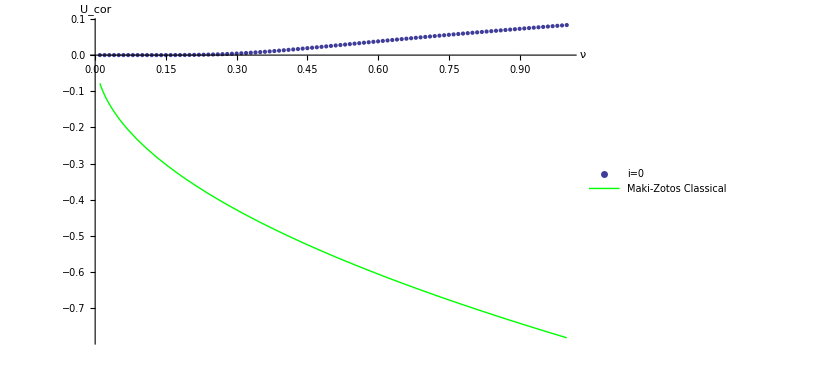

```mathematica
Show[ListPlot[Tablei0,PlotLegends->{"i=0"}],Plot[-0.78213264 √ν,{ν,0.01,1},PlotStyle->Green,PlotLegends->{"Maki-Zotos Classical"}],AxesLabel->{ν,"U_cor"},PlotRange->All,AxesOrigin->{0,0}]
```

i=1:

```mathematica
U[1]
```

1/100 √(π/5) Csch[R_ij^2/4] (BesselI[1,R_ij^2/40] Sinh[R_ij^2/40] R_ij^2+BesselI[0,R_ij^2/40] (20 Sinh[R_ij^2/40]+Cosh[R_ij^2/40] R_ij^2))

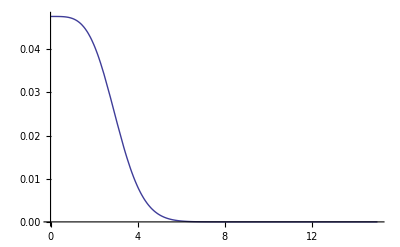

```mathematica
Plot[1/100 √(π/5) Csch[Subscript[R, ij]^2/4] (BesselI[1,Subscript[R, ij]^2/40] Sinh[Subscript[R, ij]^2/40] Subscript[R, ij]^2+BesselI[0,Subscript[R, ij]^2/40] (20 Sinh[Subscript[R, ij]^2/40]+Cosh[Subscript[R, ij]^2/40] Subscript[R, ij]^2)), {Subscript[R, ij],0,15}]
```

```mathematica
UCori1[msize_,nsize_,ν_]:=1/2∑_(m=-msize)^msize ∑_(n=-nsize)^nsize (If[R[m, n, ν]≤circleradius[msize, ν],If[m==0&&n==0,0,1/100 √(π/5) Csch[(R[m,n,ν])^2/4] (BesselI[1,(R[m,n,ν])^2/40] Sinh[(R[m,n,ν])^2/40] (R[m,n,ν])^2+BesselI[0,(R[m,n,ν])^2/40] (20 Sinh[(R[m,n,ν])^2/40]+Cosh[(R[m,n,ν])^2/40] (R[m,n,ν])^2))],0])
```

```mathematica
Tablei1=Parallelize[Table[{ν,UCori1[650,650,ν]},{ν, 0.01,1, 0.01}]]
```

{{0.01,3.12359×10^-63},{0.02,7.17887×10^-32},{0.03,1.87924×10^-21},{0.04,2.92417×10^-16},{0.05,3.72779×10^-13},{0.06,4.32003×10^-11},{0.07,1.27497×10^-9},{0.08,1.603×10^-8},{0.09,1.14229×10^-7},{0.1,5.47423×10^-7},{0.11,1.96698×10^-6},{0.12,5.69683×10^-6},{0.13,0.0000139814},{0.14,0.0000301328},{0.15,0.0000585383},{0.16,0.000104531},{0.17,0.000174152},{0.18,0.000273861},{0.19,0.000410219},{0.2,0.0005896},{0.21,0.000817937},{0.22,0.00110053},{0.23,0.00144189},{0.24,0.00184567},{0.25,0.00231463},{0.26,0.00285063},{0.27,0.00345466},{0.28,0.00412689},{0.29,0.00486678},{0.3,0.00567313},{0.31,0.00654417},{0.32,0.00747764},{0.33,0.00847093},{0.34,0.00952106},{0.35,0.0106249},{0.36,0.011779},{0.37,0.0129799},{0.38,0.0142242},{0.39,0.0155083},{0.4,0.0168286},{0.41,0.0181818},{0.42,0.0195645},{0.43,0.0209735},{0.44,0.0224056},{0.45,0.023858},{0.46,0.0253277},{0.47,0.0268122},{0.48,0.028309},{0.49,0.0298158},{0.5,0.0313303},{0.51,0.0328507},{0.52,0.0343751},{0.53,0.0359019},{0.54,0.0374294},{0.55,0.0389563},{0.56,0.0404814},{0.57,0.0420036},{0.58,0.0435218},{0.59,0.0450352},{0.6,0.0465431},{0.61,0.0480446},{0.62,0.0495394},{0.63,0.0510268},{0.64,0.0525065},{0.65,0.0539781},{0.66,0.0554415},{0.67,0.0568962},{0.68,0.0583424},{0.69,0.0597797},{0.7,0.0612083},{0.71,0.062628},{0.72,0.0640389},{0.73,0.0654411},{0.74,0.0668347},{0.75,0.0682198},{0.76,0.0695965},{0.77,0.070965},{0.78,0.0723255},{0.79,0.0736782},{0.8,0.0750233},{0.81,0.076361},{0.82,0.0776915},{0.83,0.0790151},{0.84,0.080332},{0.85,0.0816424},{0.86,0.0829467},{0.87,0.0842449},{0.88,0.0855375},{0.89,0.0868245},{0.9,0.0881063},{0.91,0.0893831},{0.92,0.0906552},{0.93,0.0919227},{0.94,0.0931858},{0.95,0.0944449},{0.96,0.0957001},{0.97,0.0969517},{0.98,0.0981997},{0.99,0.0994445},{1.,0.100686}}

```mathematica
Tablei1={{0.01,3.1235944158886063*^-63},{0.02,7.178873516155173*^-32},{0.03,1.879239046985583*^-21},{0.04,2.924166692877914*^-16},{0.05,3.72779027184479*^-13},{0.060000000000000005,4.320027303149889*^-11},{0.07,1.2749736888209213*^-9},{0.08,1.6030036733194873*^-8},{0.09,1.1422857760977053*^-7},{0.1,5.474234619567345*^-7},{0.11,1.9669756406572642*^-6},{0.12,5.696826072938237*^-6},{0.13,0.000013981366067995643},{0.14,0.00003013277051481678},{0.15,0.00005853834942223001},{0.16,0.00010453056185385256},{0.17,0.00017415209334431278},{0.18,0.0002738609289392684},{0.19,0.0004102191331901728},{0.2,0.0005896000619966219},{0.21000000000000002,0.0008179371309223661},{0.22000000000000003,0.0011005263235981536},{0.23,0.0014418859037254855},{0.24000000000000002,0.001845670695371994},{0.25,0.0023146345836592367},{0.26,0.0028506330638277265},{0.27,0.003454657190195986},{0.28,0.004126890671498896},{0.29000000000000004,0.004866782752393695},{0.30000000000000004,0.005673130643994312},{0.31000000000000005,0.006544166439967541},{0.32000000000000006,0.007477644569137776},{0.33,0.00847092683089286},{0.34,0.009521062910152707},{0.35000000000000003,0.010624864970107025},{0.36,0.011778975481971885},{0.37,0.012979927886917033},{0.38,0.014224200013999167},{0.39,0.015508260417517211},{0.4,0.01682860796459208},{0.41000000000000003,0.018181805113981087},{0.42000000000000004,0.019564505393020293},{0.43000000000000005,0.02097347561186899},{0.44000000000000006,0.02240561336165109},{0.45,0.023857960332649555},{0.46,0.025327711965917127},{0.47000000000000003,0.026812223920784365},{0.48,0.028309015805019194},{0.49,0.029815772576246093},{0.5,0.03133034398444208},{0.51,0.03285074238715781},{0.52,0.03437513923243398},{0.53,0.03590186046977031},{0.54,0.03742938111729301},{0.55,0.0389563191836427},{0.56,0.04048142911611163},{0.5700000000000001,0.042003594922168756},{0.5800000000000001,0.04352182308963094},{0.5900000000000001,0.045035235411231576},{0.6000000000000001,0.046543061802055224},{0.61,0.0480446331830683},{0.62,0.04953937449062384},{0.63,0.051026797860163745},{0.64,0.05250649602223431},{0.65,0.053978135940202815},{0.66,0.0554414527115659},{0.67,0.05689624374834787},{0.68,0.05834236324665626},{0.6900000000000001,0.05977971695089372},{0.7000000000000001,0.061208257214302876},{0.7100000000000001,0.06262797835435767},{0.7200000000000001,0.06403891229892336},{0.73,0.06544112451700984},{0.74,0.06683471022627757},{0.75,0.06821979086815705},{0.76,0.06959651084046078},{0.77,0.07096503447665443},{0.78,0.07232554326047036},{0.79,0.07367823326425425},{0.8,0.07502331279930734},{0.81,0.0763610002664871},{0.8200000000000001,0.07769152219544496},{0.8300000000000001,0.07901511146108112},{0.8400000000000001,0.08033200566607002},{0.85,0.08164244567864214},{0.86,0.08294667431517856},{0.87,0.08424493515758388},{0.88,0.08553747149582738},{0.89,0.0868245253864882},{0.9,0.08810633681859008},{0.91,0.08938314297846281},{0.92,0.09065517760582148},{0.93,0.0919226704336963},{0.9400000000000001,0.09318584670528356},{0.9500000000000001,0.09444492676121279},{0.9600000000000001,0.09570012569113491},{0.97,0.09695165304393344},{0.98,0.09819971259124279},{0.99,0.09944450213931853},{1.,0.10068621338465536}};
```

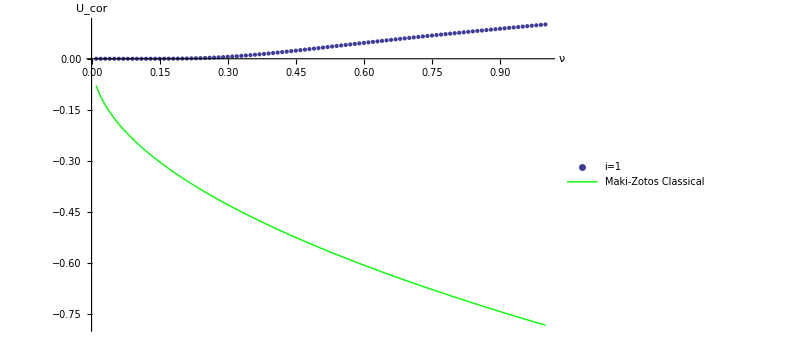

```mathematica
Show[ListPlot[Tablei1,PlotLegends->{"i=1"}],Plot[-0.78213264 √ν,{ν,0.01,1},PlotStyle->Green,PlotLegends->{"Maki-Zotos Classical"}],AxesLabel->{ν,"U_cor"},PlotRange->All,AxesOrigin->{0,0}]
```

i=2:

```mathematica
U[2]
```

1/125 Csch[R_ij^2/4] (20 Sinh[R_ij^2/20]+Cosh[R_ij^2/20] R_ij^2)

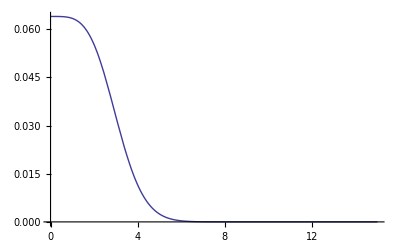

```mathematica
Plot[1/125 Csch[Subscript[R, ij]^2/4] (20 Sinh[Subscript[R, ij]^2/20]+Cosh[Subscript[R, ij]^2/20] Subscript[R, ij]^2), {Subscript[R, ij],0,15}]
```

```mathematica
UCori2[msize_,nsize_,ν_]:=1/2∑_(m=-msize)^msize ∑_(n=-nsize)^nsize (If[R[m, n, ν]≤circleradius[msize, ν],If[m==0&&n==0,0,1/125 Csch[(R[m,n,ν])^2/4] (20 Sinh[(R[m,n,ν])^2/20]+Cosh[(R[m,n,ν])^2/20] (R[m,n,ν])^2)],0])
```

```mathematica
Tablei2=Parallelize[Table[{ν,UCori2[650,650,ν]},{ν, 0.01,1, 0.01}]]
```

{{0.01,1.71722×10^-62},{0.02,2.84587×10^-31},{0.03,6.19868×10^-21},{0.04,8.5068×10^-16},{0.05,9.87188×10^-13},{0.06,1.06221×10^-10},{0.07,2.95019×10^-9},{0.08,3.52469×10^-8},{0.09,2.40418×10^-7},{0.1,1.10914×10^-6},{0.11,3.854×10^-6},{0.12,0.0000108348},{0.13,0.0000258928},{0.14,0.0000544852},{0.15,0.000103586},{0.16,0.00018139},{0.17,0.000296885},{0.18,0.000459383},{0.19,0.000678057},{0.2,0.000961542},{0.21,0.00131762},{0.22,0.00175298},{0.23,0.0022731},{0.24,0.00288216},{0.25,0.00358305},{0.26,0.0043774},{0.27,0.00526569},{0.28,0.00624734},{0.29,0.00732081},{0.3,0.00848376},{0.31,0.00973318},{0.32,0.0110655},{0.33,0.0124766},{0.34,0.0139621},{0.35,0.0155175},{0.36,0.0171379},{0.37,0.0188185},{0.38,0.0205543},{0.39,0.0223407},{0.4,0.0241728},{0.41,0.0260459},{0.42,0.0279558},{0.43,0.0298979},{0.44,0.0318684},{0.45,0.0338633},{0.46,0.035879},{0.47,0.037912},{0.48,0.0399593},{0.49,0.0420178},{0.5,0.0440848},{0.51,0.0461577},{0.52,0.0482344},{0.53,0.0503127},{0.54,0.0523908},{0.55,0.0544668},{0.56,0.0565393},{0.57,0.058607},{0.58,0.0606685},{0.59,0.062723},{0.6,0.0647694},{0.61,0.0668069},{0.62,0.068835},{0.63,0.070853},{0.64,0.0728604},{0.65,0.074857},{0.66,0.0768424},{0.67,0.0788165},{0.68,0.080779},{0.69,0.0827299},{0.7,0.0846693},{0.71,0.0865971},{0.72,0.0885134},{0.73,0.0904183},{0.74,0.092312},{0.75,0.0941947},{0.76,0.0960666},{0.77,0.097928},{0.78,0.099779},{0.79,0.10162},{0.8,0.103451},{0.81,0.105273},{0.82,0.107085},{0.83,0.108889},{0.84,0.110684},{0.85,0.112471},{0.86,0.11425},{0.87,0.116022},{0.88,0.117786},{0.89,0.119543},{0.9,0.121294},{0.91,0.123038},{0.92,0.124777},{0.93,0.126509},{0.94,0.128236},{0.95,0.129958},{0.96,0.131675},{0.97,0.133388},{0.98,0.135096},{0.99,0.1368},{1.,0.1385}}

```mathematica
Tablei2={{0.01,1.717220162202486*^-62},{0.02,2.8458724845683855*^-31},{0.03,6.1986762703401245*^-21},{0.04,8.50680235071783*^-16},{0.05,9.871882661136219*^-13},{0.060000000000000005,1.0622125290627001*^-10},{0.07,2.950191744271645*^-9},{0.08,3.524689767669546*^-8},{0.09,2.404177257437141*^-7},{0.1,1.1091407794120706*^-6},{0.11,3.853996792688027*^-6},{0.12,0.000010834797750296665},{0.13,0.00002589281345800404},{0.14,0.00005448517675744965},{0.15,0.00010358609859441083},{0.16,0.0001813895691531767},{0.17,0.00029688496487525275},{0.18,0.00045938309471372054},{0.19,0.0006780571480106223},{0.2,0.0009615424459451618},{0.21000000000000002,0.0013176186522166065},{0.22000000000000003,0.001752981922796069},{0.23,0.0022731033434406776},{0.24000000000000002,0.002882163422572079},{0.25,0.00358304932651573},{0.26,0.004377400866166206},{0.27,0.005265692045400146},{0.28,0.006247336573501093},{0.29000000000000004,0.007320807656608989},{0.30000000000000004,0.00848376432127572},{0.31000000000000005,0.009733178317930176},{0.32000000000000006,0.011065457220805038},{0.33,0.01247656065581433},{0.34,0.013962107653659604},{0.35000000000000003,0.015517473964200508},{0.36,0.01713787880977922},{0.37,0.01881846103158428},{0.38,0.020554344924730628},{0.39,0.022340696291880017},{0.4,0.024172769395520922},{0.41000000000000003,0.0260459455752311},{0.42000000000000004,0.0279557643345166},{0.43000000000000005,0.02989794770513576},{0.44000000000000006,0.031868418675413464},{0.45,0.0338633144308895},{0.46,0.03587899510680947},{0.47000000000000003,0.03791204869704013},{0.48,0.039959292706354996},{0.49,0.04201777307513361},{0.5,0.04408476084906471},{0.51,0.04615774701259525},{0.52,0.04823443585436015},{0.53,0.05031273718608144},{0.54,0.05239075769362801},{0.55,0.054466791660106505},{0.56,0.05653931126591371},{0.5700000000000001,0.058606956639450945},{0.5800000000000001,0.06066852580446767},{0.5900000000000001,0.0627229646455067},{0.6000000000000001,0.06476935699141437},{0.61,0.06680691489808463},{0.62,0.06883496919527428},{0.63,0.07085296034820347},{0.64,0.07286042967251198},{0.65,0.0748570109307593},{0.66,0.07684242232982877},{0.67,0.07881645893114916},{0.68,0.08077898547940353},{0.6900000000000001,0.0827299296502103},{0.7000000000000001,0.08466927571299918},{0.7100000000000001,0.0865970586018379},{0.7200000000000001,0.08851335838419587},{0.73,0.09041829511545045},{0.74,0.09231202406527593},{0.75,0.0941947313008214},{0.76,0.09606662961072145},{0.77,0.0979279547534285},{0.78,0.09977896201306681},{0.79,0.10161992304592866},{0.8,0.1034511230008401},{0.81,0.10527285789686693},{0.8200000000000001,0.10708543224219781},{0.8300000000000001,0.10888915687849841},{0.8400000000000001,0.11068434703555462},{0.85,0.1124713205816047},{0.86,0.11425039645537888},{0.87,0.11602189326650467},{0.88,0.11778612805159781},{0.89,0.1195434151740173},{0.9,0.12129406535592736},{0.91,0.12303838483195971},{0.92,0.12477667461441},{0.93,0.12650922986052907},{0.9400000000000001,0.12823633933306763},{0.9500000000000001,0.12995828494582196},{0.9600000000000001,0.13167534138648262},{0.97,0.13338777580962288},{0.98,0.1350958475931761},{0.99,0.13679980815222956},{1.,0.13849990080442348}};
```

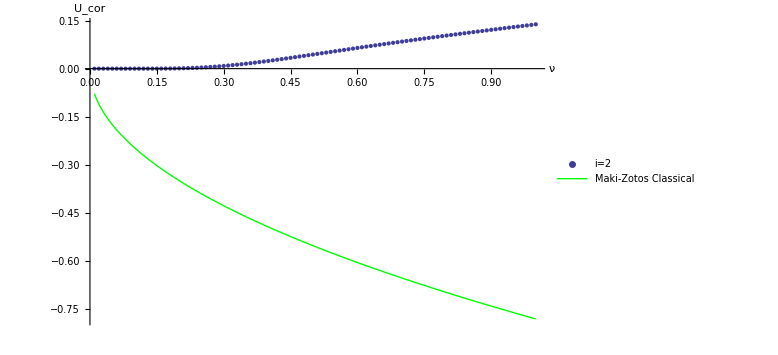

```mathematica
Show[ListPlot[Tablei2,PlotLegends->{"i=2"}],Plot[-0.78213264 √ν,{ν,0.01,1},PlotStyle->Green,PlotLegends->{"Maki-Zotos Classical"}],AxesLabel->{ν,"U_cor"},PlotRange->All,AxesOrigin->{0,0}]
```

i=3:

```mathematica
U[3]
```

1/2500 √(π/5) Csch[R_ij^2/4] (BesselI[1,R_ij^2/40] R_ij^2 (40 Sinh[R_ij^2/40]+Cosh[R_ij^2/40] R_ij^2)+BesselI[0,R_ij^2/40] (60 Cosh[R_ij^2/40] R_ij^2+Sinh[R_ij^2/40] (600+R_ij^4)))

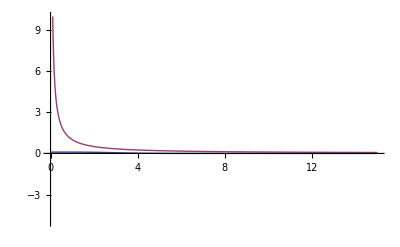

```mathematica
Plot[{1/2500 √(π/5) Csch[Subscript[R, ij]^2/4] (BesselI[1,Subscript[R, ij]^2/40] Subscript[R, ij]^2 (40 Sinh[Subscript[R, ij]^2/40]+Cosh[Subscript[R, ij]^2/40] Subscript[R, ij]^2)+BesselI[0,Subscript[R, ij]^2/40] (60 Cosh[Subscript[R, ij]^2/40] Subscript[R, ij]^2+Sinh[Subscript[R, ij]^2/40] (600+Subscript[R, ij]^4))),1/Subscript[R, ij]}, {Subscript[R, ij],0,15}, PlotRange->{-5,10}]
```

```mathematica
UCori3[msize_,nsize_,ν_]:=1/2∑_(m=-msize)^msize ∑_(n=-nsize)^nsize (If[R[m, n, ν]≤circleradius[msize, ν],If[m==0&&n==0,0,1/2500 √(π/5) Csch[(R[m,n,ν])^2/4] (BesselI[1,(R[m,n,ν])^2/40] (R[m,n,ν])^2 (40 Sinh[(R[m,n,ν])^2/40]+Cosh[(R[m,n,ν])^2/40] (R[m,n,ν])^2)+BesselI[0,(R[m,n,ν])^2/40] (60 Cosh[(R[m,n,ν])^2/40] (R[m,n,ν])^2+Sinh[(R[m,n,ν])^2/40] (600+(R[m,n,ν])^4)))],0])
```

```mathematica
Tablei3=Parallelize[Table[{ν,UCori3[650,650,ν]},{ν, 0.01,1, 0.01}]]
```

{{0.01,9.56297×10^-62},{0.02,1.15575×10^-30},{0.03,2.11546×10^-20},{0.04,2.58293×10^-15},{0.05,2.74975×10^-12},{0.06,2.76618×10^-10},{0.07,7.27507×10^-9},{0.08,8.30572×10^-8},{0.09,5.45041×10^-7},{0.1,2.43169×10^-6},{0.11,8.20484×10^-6},{0.12,0.0000224725},{0.13,0.0000524643},{0.14,0.000108097},{0.15,0.000201621},{0.16,0.000346963},{0.17,0.000558912},{0.18,0.000852289},{0.19,0.00124121},{0.2,0.00173851},{0.21,0.00235527},{0.22,0.00310062},{0.23,0.00398153},{0.24,0.0050029},{0.25,0.00616755},{0.26,0.0074764},{0.27,0.00892867},{0.28,0.010522},{0.29,0.0122529},{0.3,0.0141165},{0.31,0.0161073},{0.32,0.018219},{0.33,0.0204448},{0.34,0.0227774},{0.35,0.0252094},{0.36,0.0277334},{0.37,0.0303418},{0.38,0.0330272},{0.39,0.0357822},{0.4,0.0385997},{0.41,0.0414729},{0.42,0.0443954},{0.43,0.0473608},{0.44,0.0503633},{0.45,0.0533974},{0.46,0.0564579},{0.47,0.05954},{0.48,0.0626393},{0.49,0.0657516},{0.5,0.0688731},{0.51,0.0720005},{0.52,0.0751306},{0.53,0.0782606},{0.54,0.0813879},{0.55,0.0845103},{0.56,0.0876257},{0.57,0.0907324},{0.58,0.0938289},{0.59,0.0969136},{0.6,0.0999856},{0.61,0.103044},{0.62,0.106087},{0.63,0.109116},{0.64,0.112128},{0.65,0.115125},{0.66,0.118105},{0.67,0.121068},{0.68,0.124014},{0.69,0.126944},{0.7,0.129856},{0.71,0.132753},{0.72,0.135632},{0.73,0.138496},{0.74,0.141343},{0.75,0.144175},{0.76,0.146992},{0.77,0.149793},{0.78,0.152581},{0.79,0.155354},{0.8,0.158113},{0.81,0.160859},{0.82,0.163592},{0.83,0.166313},{0.84,0.169023},{0.85,0.17172},{0.86,0.174407},{0.87,0.177083},{0.88,0.179749},{0.89,0.182406},{0.9,0.185053},{0.91,0.187692},{0.92,0.190323},{0.93,0.192945},{0.94,0.19556},{0.95,0.198168},{0.96,0.200769},{0.97,0.203364},{0.98,0.205953},{0.99,0.208536},{1.,0.211114}}

```mathematica
Tablei3={{0.01,9.562970336710711*^-62},{0.02,1.1557526060258763*^-30},{0.03,2.1154634411186947*^-20},{0.04,2.5829301324064986*^-15},{0.05,2.7497474757367863*^-12},{0.060000000000000005,2.7661780472996184*^-10},{0.07,7.27506680149373*^-9},{0.08,8.305720814517375*^-8},{0.09,5.450407788327194*^-7},{0.1,2.4316931461902*^-6},{0.11,8.204835544057543*^-6},{0.12,0.000022472454920364682},{0.13,0.000052464264123001984},{0.14,0.00010809665120058745},{0.15,0.00020162077624059558},{0.16,0.00034696312975826505},{0.17,0.0005589117799237435},{0.18,0.000852289438516899},{0.19,0.0012412149338493902},{0.2,0.0017385103811996354},{0.21000000000000002,0.002355274493873403},{0.22000000000000003,0.0031006170243264943},{0.23,0.003981534576696532},{0.24000000000000002,0.005002901474134537},{0.25,0.0061675482535864},{0.26,0.007476402421387729},{0.27,0.008928669702003521},{0.28,0.01052203809640705},{0.29000000000000004,0.01225289102397982},{0.30000000000000004,0.014116519342164438},{0.31000000000000005,0.016107325000971288},{0.32000000000000006,0.01821901148427686},{0.33,0.020444758063274438},{0.34,0.022777376310701283},{0.35000000000000003,0.025209448374690455},{0.36,0.027733447261373643},{0.37,0.030341839890175498},{0.38,0.03302717401953807},{0.39,0.03578215033816862},{0.4,0.03859968111348907},{0.41000000000000003,0.04147293681284218},{0.42000000000000004,0.04439538208589343},{0.43000000000000005,0.04736080243515102},{0.44000000000000006,0.05036332281809196},{0.45,0.05339741932830526},{0.46,0.05645792500109228},{0.47000000000000003,0.05954003068593349},{0.48,0.06263928182749325},{0.49,0.06575157190063305},{0.5,0.0688731331546562},{0.51,0.07200052523851802},{0.52,0.07513062220236584},{0.53,0.07826059830157536},{0.54,0.08138791296724626},{0.55,0.08451029525160611},{0.56,0.08762572800753382},{0.5700000000000001,0.09073243201799565},{0.5800000000000001,0.09382885025311659},{0.5900000000000001,0.09691363239939328},{0.6000000000000001,0.09998561977673295},{0.61,0.10304383073411387},{0.62,0.10608744659329931},{0.63,0.109115798191785},{0.64,0.11212835306067985},{0.65,0.11512470326016627},{0.66,0.11810455388425821},{0.67,0.12106771223752293},{0.68,0.12401407767898266},{0.6900000000000001,0.1269436321223818},{0.7000000000000001,0.1298564311771707},{0.7100000000000001,0.1327525959107748},{0.7200000000000001,0.13563230520982025},{0.73,0.13849578871584203},{0.74,0.14134332030950766},{0.75,0.14417521211642362},{0.76,0.1469918090070827},{0.77,0.1497934835633742},{0.78,0.15258063148424397},{0.79,0.15535366740350892},{0.8,0.15811302109344672},{0.81,0.16085913402854946},{0.8200000000000001,0.16359245628471863},{0.8300000000000001,0.16631344375016152},{0.8400000000000001,0.1690225556252838},{0.85,0.1717202521899569},{0.86,0.1744069928176411},{0.87,0.1770832342169525},{0.88,0.17974942888236833},{0.89,0.18240602373685097},{0.9,0.18505345895023778},{0.91,0.1876921669182728},{0.92,0.19032257138816397},{0.93,0.19294508671750013},{0.9400000000000001,0.19556011725428873},{0.9500000000000001,0.1981680568267496},{0.9600000000000001,0.20076928833233113},{0.97,0.20336418341620519},{0.98,0.2059531022302445},{0.99,0.20853639326418155},{1.,0.21111439324131442}};
```

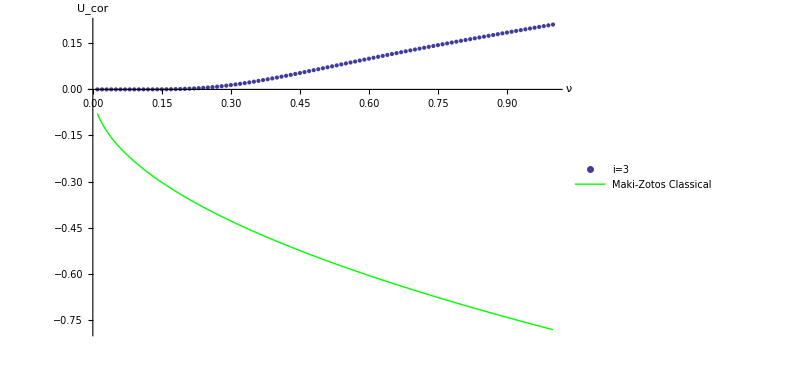

```mathematica
Show[ListPlot[Tablei3,PlotLegends->{"i=3"}],Plot[-0.78213264 √ν,{ν,0.01,1},PlotStyle->Green,PlotLegends->{"Maki-Zotos Classical"}],AxesLabel->{ν,"U_cor"},PlotRange->All,AxesOrigin->{0,0}]
```

i=4:

```mathematica
U[4]
```

(Csch[R_ij^2/4] (80 Cosh[R_ij^2/20] R_ij^2+Sinh[R_ij^2/20] (800+R_ij^4)))/3125

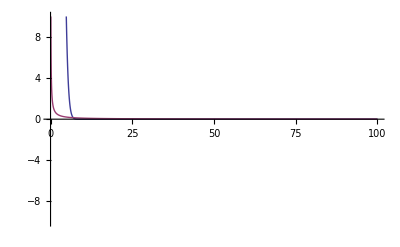

```mathematica
Plot[{1000(Csch[Subscript[R, ij]^2/4] (80 Cosh[Subscript[R, ij]^2/20] Subscript[R, ij]^2+Sinh[Subscript[R, ij]^2/20] (800+Subscript[R, ij]^4)))/3125,1/Subscript[R, ij]}, {Subscript[R, ij],0,100}, PlotRange->{-10,10}]
```

```mathematica
UCori4[msize_,nsize_,ν_]:=1/2∑_(m=-msize)^msize ∑_(n=-nsize)^nsize (If[R[m, n, ν]≤circleradius[msize, ν],If[m==0&&n==0,0,1/3125 Csch[(R[m,n,ν])^2/4] (80 Cosh[(R[m,n,ν])^2/20](R[m,n,ν])^2+Sinh[(R[m,n,ν])^2/20] (800+(R[m,n,ν])^4))],0])
```

```mathematica
Tablei4=Parallelize[Table[{ν,UCori4[650,650,ν]},{ν, 0.01,1, 0.01}]]
```

{{0.01,5.39196×10^-61},{0.02,4.80059×10^-30},{0.03,7.44615×10^-20},{0.04,8.1459×10^-15},{0.05,8.00338×10^-12},{0.06,7.56637×10^-10},{0.07,1.89292×10^-8},{0.08,2.07341×10^-7},{0.09,1.31373×10^-6},{0.1,5.68664×10^-6},{0.11,0.0000186867},{0.12,0.0000499972},{0.13,0.000114305},{0.14,0.000231107},{0.15,0.000423731},{0.16,0.000717856},{0.17,0.00113988},{0.18,0.00171536},{0.19,0.00246777},{0.2,0.00341757},{0.21,0.0045816},{0.22,0.0059728},{0.23,0.00760024},{0.24,0.00946917},{0.25,0.0115814},{0.26,0.0139356},{0.27,0.0165276},{0.28,0.0193511},{0.29,0.0223978},{0.3,0.0256578},{0.31,0.0291202},{0.32,0.0327731},{0.33,0.0366039},{0.34,0.0405999},{0.35,0.0447483},{0.36,0.0490361},{0.37,0.0534506},{0.38,0.0579796},{0.39,0.062611},{0.4,0.0673334},{0.41,0.0721359},{0.42,0.0770081},{0.43,0.0819403},{0.44,0.0869235},{0.45,0.091949},{0.46,0.0970091},{0.47,0.102096},{0.48,0.107204},{0.49,0.112327},{0.5,0.117458},{0.51,0.122593},{0.52,0.127728},{0.53,0.132858},{0.54,0.13798},{0.55,0.14309},{0.56,0.148186},{0.57,0.153266},{0.58,0.158327},{0.59,0.163367},{0.6,0.168385},{0.61,0.17338},{0.62,0.178351},{0.63,0.183296},{0.64,0.188216},{0.65,0.19311},{0.66,0.197977},{0.67,0.202818},{0.68,0.207633},{0.69,0.212421},{0.7,0.217183},{0.71,0.221919},{0.72,0.22663},{0.73,0.231316},{0.74,0.235977},{0.75,0.240615},{0.76,0.245229},{0.77,0.24982},{0.78,0.25439},{0.79,0.258939},{0.8,0.263466},{0.81,0.267974},{0.82,0.272463},{0.83,0.276934},{0.84,0.281386},{0.85,0.285822},{0.86,0.290241},{0.87,0.294645},{0.88,0.299034},{0.89,0.303409},{0.9,0.30777},{0.91,0.312118},{0.92,0.316454},{0.93,0.320779},{0.94,0.325092},{0.95,0.329396},{0.96,0.333689},{0.97,0.337973},{0.98,0.342248},{0.99,0.346515},{1.,0.350774}}

```mathematica
Tablei4={{0.01,5.391955961957999*^-61},{0.02,4.800586538019848*^-30},{0.03,7.446154024402039*^-20},{0.04,8.145897430190758*^-15},{0.05,8.003377149515402*^-12},{0.060000000000000005,7.566374531034197*^-10},{0.07,1.8929182782176464*^-8},{0.08,2.0734144360623982*^-7},{0.09,1.3137295644534753*^-6},{0.1,5.686639229988056*^-6},{0.11,0.000018686685237686292},{0.12,0.000049997154318362595},{0.13,0.00011430503488927854},{0.14,0.0002311073172832656},{0.15,0.0004237309167764051},{0.16,0.0007178563415493659},{0.17,0.001139876416504271},{0.18,0.0017153579439620583},{0.19,0.0024677728990093136},{0.2,0.0034175709219577254},{0.21000000000000002,0.004581595519314924},{0.22000000000000003,0.005972804877451621},{0.23,0.007600239155435728},{0.24000000000000002,0.009469172255389638},{0.25,0.01158139094422151},{0.26,0.013935553152945332},{0.27,0.016527587345411855},{0.28,0.01935110437410539},{0.29000000000000004,0.02239780145627514},{0.30000000000000004,0.02565784457327154},{0.31000000000000005,0.029120220773624306},{0.32000000000000006,0.03277305573416722},{0.33,0.03660389473440404},{0.34,0.04059994715322888},{0.35000000000000003,0.044748295902911066},{0.36,0.04903607403764006},{0.37,0.05345061124395045},{0.38,0.0579795531394111},{0.39,0.06261095635083277},{0.4,0.06733336227103315},{0.41000000000000003,0.07213585224575403},{0.42000000000000004,0.07700808674985014},{0.43000000000000005,0.08194033089582005},{0.44000000000000006,0.08692346839308238},{0.45,0.09194900585329664},{0.46,0.0970090691221741},{0.47000000000000003,0.1020963931158113},{0.48,0.10720430645199046},{0.49,0.11232671199526356},{0.5,0.11745806427922084},{0.51,0.12259334462982172},{0.52,0.12772803468932012},{0.53,0.13285808893021794},{0.54,0.13797990665174822},{0.55,0.14309030386652263},{0.56,0.14818648541104054},{0.5700000000000001,0.15326601754966143},{0.5800000000000001,0.15832680128636406},{0.5900000000000001,0.16336704655116774},{0.6000000000000001,0.16838524738759297},{0.61,0.17338015823315464},{0.62,0.1783507713558855},{0.63,0.18329629548558202},{0.64,0.18821613565826978},{0.65,0.1931098742757491},{0.66,0.19797725336851524},{0.67,0.20281815803945236},{0.68,0.20763260105706466},{0.6900000000000001,0.21242070856033296},{0.7000000000000001,0.21718270683225485},{0.7100000000000001,0.22191891009550346},{0.7200000000000001,0.22662970928118956},{0.73,0.23131556172024542},{0.74,0.2359769817063031},{0.75,0.2406145318789544},{0.76,0.2452288153768484},{0.77,0.249820468711081},{0.78,0.25439015531067216},{0.79,0.2589385596935416},{0.8,0.2634663822181966},{0.81,0.267974334373296},{0.8200000000000001,0.2724631345642947},{0.8300000000000001,0.27693350435848074},{0.8400000000000001,0.28138616515182446},{0.85,0.28582183522318333},{0.86,0.2902412271434975},{0.87,0.29464504550964576},{0.88,0.2990339849746366},{0.89,0.30340872854771317},{0.9,0.30776994613981135},{0.91,0.3121182933315631},{0.92,0.3164544103427263},{0.93,0.32077892118351026},{0.9400000000000001,0.32509243296977386},{0.9500000000000001,0.3293955353854983},{0.9600000000000001,0.3336888002772586},{0.97,0.3379727813666816},{0.98,0.34224801406803934},{0.99,0.34651501539921686},{1.,0.3507742839753128}};
```

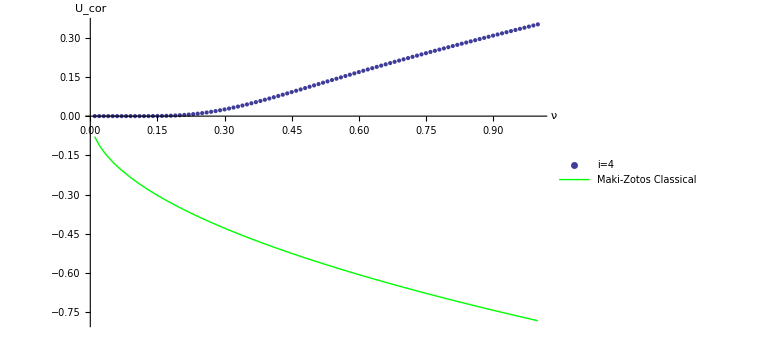

```mathematica
Show[ListPlot[Tablei4,PlotLegends->{"i=4"}],Plot[-0.78213264 √ν,{ν,0.01,1},PlotStyle->Green,PlotLegends->{"Maki-Zotos Classical"}],AxesLabel->{ν,"U_cor"},PlotRange->All,AxesOrigin->{0,0}]
```

Notice that as i increases, the value of the two-body potential at R=0 increases, and the curve is larger overall.  Thus the energy contribution increases as i increases.  ν and R are inversely related.  The value of i_max cannot be too high.